```mathematica
EulerianGraphQManual[graph_?GraphQ]:=AllTrue[VertexDegree[graph],EvenQ]
```

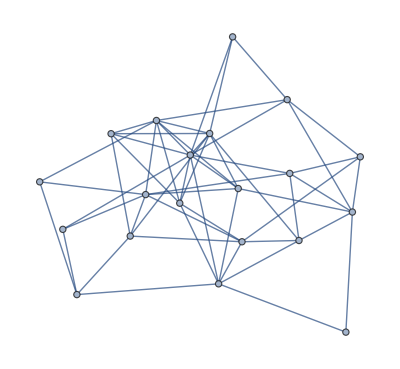

```mathematica
testgraph=RandomGraph[{20,54}]
```

```mathematica
EulerianGraphQ[testgraph]
```

False

```mathematica
EulerianGraphQManual[testgraph]
```

False

```mathematica
EulerizeGraph[testgraph]
```

-Graphics-

```mathematica
EulerianGraphQManual[EulerizeGraph[testgraph]]
```

True

```mathematica
PrintDefinitions["EulerianGraphQ"]
```

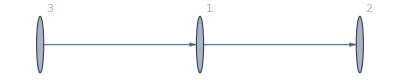

```mathematica
Graph[{1->2,3->1},VertexLabels->Automatic]
```

```mathematica
Thread[Range[3]->VertexDegree[Graph[{1->2,3->1},VertexLabels->Automatic]]]
```

{1→2,2→1,3→1}

```mathematica
EulerianGraphQManual[Graph[{1->2,3->1},VertexLabels->Automatic]]
```

False

```mathematica
EulerianGraphQManual[Graph[{1->2,2->3,3->1},VertexLabels->Automatic]]
```

True

## Linear Optimization Example

```mathematica
weights=Block[{n=10},SeedRandom[123];RandomReal[1,{n,n}]];
```

```mathematica
cost = Total[weights*x, 2];
```

```mathematica
constraints={Total[x]==1,Total[x,{2}]==1,x\[VectorGreaterEqual]0};
```

```mathematica
{minCost,rule}=LinearOptimization[cost,constraints,x∈Matrices[Dimensions[weights]],{"PrimalMinimumValue","PrimalMinimizerRules"}]
```

{1.55934,{x→{{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.}}}}

```mathematica
graph=AdjacencyGraph[Round[x/. rule]]
```

-Graphics-

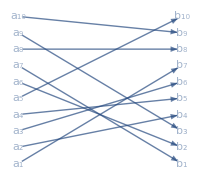

```mathematica
edges=EdgeList[graph]/. DirectedEdge[i_,j_]:>DirectedEdge[Subscript[a,i],Subscript[b,j]];
Graph[edges,Sequence[VertexShapeFunction->"Name",VertexCoordinates->Flatten[Table[{Subscript[a,i]->{0,0.1 i},Subscript[b,i]->{1,0.1 i}},{i,Length[weights]}]],ImageSize->200]]
```

```mathematica
Groupings[Array[Indexed[x,{##}]&,2],2]
```

{{x1,x2}}

```mathematica
Groupings[Array[Indexed[x,{##}]&,4],2]
```

{{{{x1,x2},x3},x4},{x1,{{x2,x3},x4}},{{x1,{x2,x3}},x4},{x1,{x2,{x3,x4}}},{{x1,x2},{x3,x4}}}

```mathematica
Groupings[Array[Indexed[x,{##}]&,4],List->{2,Orderless}]
```

{{{{x1,x2},x3},x4},{{x1,x2},{x3,x4}}}

```mathematica
Subsets[Array[Indexed[x,{##}]&,4],2]
```

{{},{x1},{x2},{x3},{x4},{x1,x2},{x1,x3},{x1,x4},{x2,x3},{x2,x4},{x3,x4}}

```mathematica
Tuples[Array[Indexed[x,{##}]&,4],2]
```

{{x1,x1},{x1,x2},{x1,x3},{x1,x4},{x2,x1},{x2,x2},{x2,x3},{x2,x4},{x3,x1},{x3,x2},{x3,x3},{x3,x4},{x4,x1},{x4,x2},{x4,x3},{x4,x4}}

```mathematica
Array[Indexed[x,{##}]&,4]
```

{x1,x2,x3,x4}

```mathematica
{{Subscript[x, 1],Subscript[x, 2]},{Subscript[x, 3],Subscript[x, 4]}}
```

```mathematica
{{Subscript[x, 2],Subscript[x, 4]},{Subscript[x, 3],Subscript[x, 1]}}
```

{{x_1,x_3},{x_3,x_1}}

```mathematica
Permutations[Array[Indexed[x,{##}]&,4],{2}]
```

{{x1,x2},{x1,x3},{x1,x4},{x2,x1},{x2,x3},{x2,x4},{x3,x1},{x3,x2},{x3,x4},{x4,x1},{x4,x2},{x4,x3}}

```mathematica
Tuples[Permutations[Array[Indexed[x,{##}]&,4],{2}],{2}]
```

{{{x1,x2},{x1,x2}},{{x1,x2},{x1,x3}},{{x1,x2},{x1,x4}},{{x1,x2},{x2,x1}},{{x1,x2},{x2,x3}},{{x1,x2},{x2,x4}},{{x1,x2},{x3,x1}},{{x1,x2},{x3,x2}},{{x1,x2},{x3,x4}},{{x1,x2},{x4,x1}},{{x1,x2},{x4,x2}},{{x1,x2},{x4,x3}},{{x1,x3},{x1,x2}},{{x1,x3},{x1,x3}},{{x1,x3},{x1,x4}},{{x1,x3},{x2,x1}},{{x1,x3},{x2,x3}},{{x1,x3},{x2,x4}},{{x1,x3},{x3,x1}},{{x1,x3},{x3,x2}},{{x1,x3},{x3,x4}},{{x1,x3},{x4,x1}},{{x1,x3},{x4,x2}},{{x1,x3},{x4,x3}},{{x1,x4},{x1,x2}},{{x1,x4},{x1,x3}},{{x1,x4},{x1,x4}},{{x1,x4},{x2,x1}},{{x1,x4},{x2,x3}},{{x1,x4},{x2,x4}},{{x1,x4},{x3,x1}},{{x1,x4},{x3,x2}},{{x1,x4},{x3,x4}},{{x1,x4},{x4,x1}},{{x1,x4},{x4,x2}},{{x1,x4},{x4,x3}},{{x2,x1},{x1,x2}},{{x2,x1},{x1,x3}},{{x2,x1},{x1,x4}},{{x2,x1},{x2,x1}},{{x2,x1},{x2,x3}},{{x2,x1},{x2,x4}},{{x2,x1},{x3,x1}},{{x2,x1},{x3,x2}},{{x2,x1},{x3,x4}},{{x2,x1},{x4,x1}},{{x2,x1},{x4,x2}},{{x2,x1},{x4,x3}},{{x2,x3},{x1,x2}},{{x2,x3},{x1,x3}},{{x2,x3},{x1,x4}},{{x2,x3},{x2,x1}},{{x2,x3},{x2,x3}},{{x2,x3},{x2,x4}},{{x2,x3},{x3,x1}},{{x2,x3},{x3,x2}},{{x2,x3},{x3,x4}},{{x2,x3},{x4,x1}},{{x2,x3},{x4,x2}},{{x2,x3},{x4,x3}},{{x2,x4},{x1,x2}},{{x2,x4},{x1,x3}},{{x2,x4},{x1,x4}},{{x2,x4},{x2,x1}},{{x2,x4},{x2,x3}},{{x2,x4},{x2,x4}},{{x2,x4},{x3,x1}},{{x2,x4},{x3,x2}},{{x2,x4},{x3,x4}},{{x2,x4},{x4,x1}},{{x2,x4},{x4,x2}},{{x2,x4},{x4,x3}},{{x3,x1},{x1,x2}},{{x3,x1},{x1,x3}},{{x3,x1},{x1,x4}},{{x3,x1},{x2,x1}},{{x3,x1},{x2,x3}},{{x3,x1},{x2,x4}},{{x3,x1},{x3,x1}},{{x3,x1},{x3,x2}},{{x3,x1},{x3,x4}},{{x3,x1},{x4,x1}},{{x3,x1},{x4,x2}},{{x3,x1},{x4,x3}},{{x3,x2},{x1,x2}},{{x3,x2},{x1,x3}},{{x3,x2},{x1,x4}},{{x3,x2},{x2,x1}},{{x3,x2},{x2,x3}},{{x3,x2},{x2,x4}},{{x3,x2},{x3,x1}},{{x3,x2},{x3,x2}},{{x3,x2},{x3,x4}},{{x3,x2},{x4,x1}},{{x3,x2},{x4,x2}},{{x3,x2},{x4,x3}},{{x3,x4},{x1,x2}},{{x3,x4},{x1,x3}},{{x3,x4},{x1,x4}},{{x3,x4},{x2,x1}},{{x3,x4},{x2,x3}},{{x3,x4},{x2,x4}},{{x3,x4},{x3,x1}},{{x3,x4},{x3,x2}},{{x3,x4},{x3,x4}},{{x3,x4},{x4,x1}},{{x3,x4},{x4,x2}},{{x3,x4},{x4,x3}},{{x4,x1},{x1,x2}},{{x4,x1},{x1,x3}},{{x4,x1},{x1,x4}},{{x4,x1},{x2,x1}},{{x4,x1},{x2,x3}},{{x4,x1},{x2,x4}},{{x4,x1},{x3,x1}},{{x4,x1},{x3,x2}},{{x4,x1},{x3,x4}},{{x4,x1},{x4,x1}},{{x4,x1},{x4,x2}},{{x4,x1},{x4,x3}},{{x4,x2},{x1,x2}},{{x4,x2},{x1,x3}},{{x4,x2},{x1,x4}},{{x4,x2},{x2,x1}},{{x4,x2},{x2,x3}},{{x4,x2},{x2,x4}},{{x4,x2},{x3,x1}},{{x4,x2},{x3,x2}},{{x4,x2},{x3,x4}},{{x4,x2},{x4,x1}},{{x4,x2},{x4,x2}},{{x4,x2},{x4,x3}},{{x4,x3},{x1,x2}},{{x4,x3},{x1,x3}},{{x4,x3},{x1,x4}},{{x4,x3},{x2,x1}},{{x4,x3},{x2,x3}},{{x4,x3},{x2,x4}},{{x4,x3},{x3,x1}},{{x4,x3},{x3,x2}},{{x4,x3},{x3,x4}},{{x4,x3},{x4,x1}},{{x4,x3},{x4,x2}},{{x4,x3},{x4,x3}}}

```mathematica
Groupings[Array[Indexed[x,{##}]&,4],2]
```

{{{{x1,x2},x3},x4},{x1,{{x2,x3},x4}},{{x1,{x2,x3}},x4},{x1,{x2,{x3,x4}}},{{x1,x2},{x3,x4}}}

```mathematica
Groupings[Array[Indexed[x,{##}]&,4],f->2]
```

{f[f[f[x1,x2],x3],x4],f[x1,f[f[x2,x3],x4]],f[f[x1,f[x2,x3]],x4],f[x1,f[x2,f[x3,x4]]],f[f[x1,x2],f[x3,x4]]}

```mathematica
Partition[{x1,x2},2]
```

{{x1,x2}}

```mathematica
Partition[{x1,x2,x3},2]
```

{{x1,x2}}

```mathematica
Permutations[Array[Indexed[x,{##}]&,4]]
```

{{x1,x2,x3,x4},{x1,x2,x4,x3},{x1,x3,x2,x4},{x1,x3,x4,x2},{x1,x4,x2,x3},{x1,x4,x3,x2},{x2,x1,x3,x4},{x2,x1,x4,x3},{x2,x3,x1,x4},{x2,x3,x4,x1},{x2,x4,x1,x3},{x2,x4,x3,x1},{x3,x1,x2,x4},{x3,x1,x4,x2},{x3,x2,x1,x4},{x3,x2,x4,x1},{x3,x4,x1,x2},{x3,x4,x2,x1},{x4,x1,x2,x3},{x4,x1,x3,x2},{x4,x2,x1,x3},{x4,x2,x3,x1},{x4,x3,x1,x2},{x4,x3,x2,x1}}

```mathematica
Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,4]]
```

{{{x1,x2},{x3,x4}},{{x1,x2},{x4,x3}},{{x1,x3},{x2,x4}},{{x1,x3},{x4,x2}},{{x1,x4},{x2,x3}},{{x1,x4},{x3,x2}},{{x2,x1},{x3,x4}},{{x2,x1},{x4,x3}},{{x2,x3},{x1,x4}},{{x2,x3},{x4,x1}},{{x2,x4},{x1,x3}},{{x2,x4},{x3,x1}},{{x3,x1},{x2,x4}},{{x3,x1},{x4,x2}},{{x3,x2},{x1,x4}},{{x3,x2},{x4,x1}},{{x3,x4},{x1,x2}},{{x3,x4},{x2,x1}},{{x4,x1},{x2,x3}},{{x4,x1},{x3,x2}},{{x4,x2},{x1,x3}},{{x4,x2},{x3,x1}},{{x4,x3},{x1,x2}},{{x4,x3},{x2,x1}}}

```mathematica
Sort/@Permutations[Array[Indexed[x,{##}]&,4]]
```

{{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4},{x1,x2,x3,x4}}

```mathematica
Union[Sort/@Permutations[Array[Indexed[x,{##}]&,4]]]
```

{{x1,x2,x3,x4}}

```mathematica
Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,4]]
```

{{{x1,x2},{x3,x4}},{{x1,x2},{x3,x4}},{{x1,x3},{x2,x4}},{{x1,x3},{x2,x4}},{{x1,x4},{x2,x3}},{{x1,x4},{x2,x3}},{{x1,x2},{x3,x4}},{{x1,x2},{x3,x4}},{{x2,x3},{x1,x4}},{{x2,x3},{x1,x4}},{{x2,x4},{x1,x3}},{{x2,x4},{x1,x3}},{{x1,x3},{x2,x4}},{{x1,x3},{x2,x4}},{{x2,x3},{x1,x4}},{{x2,x3},{x1,x4}},{{x3,x4},{x1,x2}},{{x3,x4},{x1,x2}},{{x1,x4},{x2,x3}},{{x1,x4},{x2,x3}},{{x2,x4},{x1,x3}},{{x2,x4},{x1,x3}},{{x3,x4},{x1,x2}},{{x3,x4},{x1,x2}}}

```mathematica
Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,4]]]
```

{{{x1,x2},{x3,x4}},{{x1,x3},{x2,x4}},{{x1,x4},{x2,x3}},{{x2,x3},{x1,x4}},{{x2,x4},{x1,x3}},{{x3,x4},{x1,x2}}}

```mathematica
Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,4]]]
```

{{{x1,x2},{x3,x4}},{{x1,x3},{x2,x4}},{{x1,x4},{x2,x3}},{{x1,x4},{x2,x3}},{{x1,x3},{x2,x4}},{{x1,x2},{x3,x4}}}

```mathematica
Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,4]]]]
```

{{{x1,x2},{x3,x4}},{{x1,x3},{x2,x4}},{{x1,x4},{x2,x3}}}

```mathematica
TimeConstrained[RepeatedTiming@Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,{##}]&,100]]]],20]
```

Permutations::fac: In Permutations[{x,x,x,x,x,x,x,x,x,x,«90»}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

Permutations::fac: In Permutations[{{x,x},{x,x},{x,x},{x,x},{x,x},{x,x},{x,x},{x,x},{x,x},{x,x},«40»}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

General::stop: Further output of Permutations::fac will be suppressed during this calculation.

{0.000143563,Permutations[{{x1,x2},{x3,x4},{x5,x6},{x7,x8},{x9,x10},{x11,x12},{x13,x14},{x15,x16},{x17,x18},{x19,x20},{x21,x22},{x23,x24},{x25,x26},{x27,x28},{x29,x30},{x31,x32},{x33,x34},{x35,x36},{x37,x38},{x39,x40},{x41,x42},{x43,x44},{x45,x46},{x47,x48},{x49,x50},{x51,x52},{x53,x54},{x55,x56},{x57,x58},{x59,x60},{x61,x62},{x63,x64},{x65,x66},{x67,x68},{x69,x70},{x71,x72},{x73,x74},{x75,x76},{x77,x78},{x79,x80},{x81,x82},{x83,x84},{x85,x86},{x87,x88},{x89,x90},{x91,x92},{x93,x94},{x95,x96},{x97,x98},{x99,x100}}]}

```mathematica
Permutations[Array[Indexed[x,{##}]&,4]]
```

{{x1,x2,x3,x4},{x1,x2,x4,x3},{x1,x3,x2,x4},{x1,x3,x4,x2},{x1,x4,x2,x3},{x1,x4,x3,x2},{x2,x1,x3,x4},{x2,x1,x4,x3},{x2,x3,x1,x4},{x2,x3,x4,x1},{x2,x4,x1,x3},{x2,x4,x3,x1},{x3,x1,x2,x4},{x3,x1,x4,x2},{x3,x2,x1,x4},{x3,x2,x4,x1},{x3,x4,x1,x2},{x3,x4,x2,x1},{x4,x1,x2,x3},{x4,x1,x3,x2},{x4,x2,x1,x3},{x4,x2,x3,x1},{x4,x3,x1,x2},{x4,x3,x2,x1}}

```mathematica
Subsets[Array[Indexed[x,{##}]&,4],{2}]
```

{{x1,x2},{x1,x3},{x1,x4},{x2,x3},{x2,x4},{x3,x4}}

```mathematica
Subsets[Subsets[Array[Indexed[x,{##}]&,4],{2}],{2}]
```

{{{x1,x2},{x1,x3}},{{x1,x2},{x1,x4}},{{x1,x2},{x2,x3}},{{x1,x2},{x2,x4}},{{x1,x2},{x3,x4}},{{x1,x3},{x1,x4}},{{x1,x3},{x2,x3}},{{x1,x3},{x2,x4}},{{x1,x3},{x3,x4}},{{x1,x4},{x2,x3}},{{x1,x4},{x2,x4}},{{x1,x4},{x3,x4}},{{x2,x3},{x2,x4}},{{x2,x3},{x3,x4}},{{x2,x4},{x3,x4}}}

```mathematica
IntegerPartitions[4,{2}]
```

{{3,1},{2,2}}

```mathematica
myList={a,b,c,d,e,f}
```

{a,b,c,d,e,f}

```mathematica
g[{},_,out_]:=out
g[in_,breaks_,out_]:=g[Drop[in,First@breaks],Rest@breaks,Append[out,Take[in,First@breaks]]]
```

```mathematica
g[myList,#,{}]&/@IntegerPartitions[Length[myList]]//MatrixForm
```

({{a,b,c,d,e,f}}
{{a,b,c,d,e},{f}}
{{a,b,c,d},{e,f}}
{{a,b,c,d},{e},{f}}
{{a,b,c},{d,e,f}}
{{a,b,c},{d,e},{f}}
{{a,b,c},{d},{e},{f}}
{{a,b},{c,d},{e,f}}
{{a,b},{c,d},{e},{f}}
{{a,b},{c},{d},{e},{f}}
{{a},{b},{c},{d},{e},{f}})

```mathematica
BipartiteGraphQ[CompleteGraph[5]]
```

False

```mathematica
BipartiteGraphQ[CompleteGraph[4]]
```

False

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

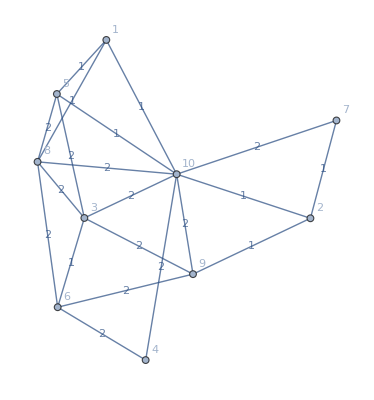

```mathematica
randomGraph=RandomWeightedMixedGraph[{10,20},0,RandomInteger[{1,2}]&,VertexLabels->Automatic,EdgeLabels->"EdgeWeight"]
```

```mathematica
VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]
```

{1,2,3,9,11,13,16,17}

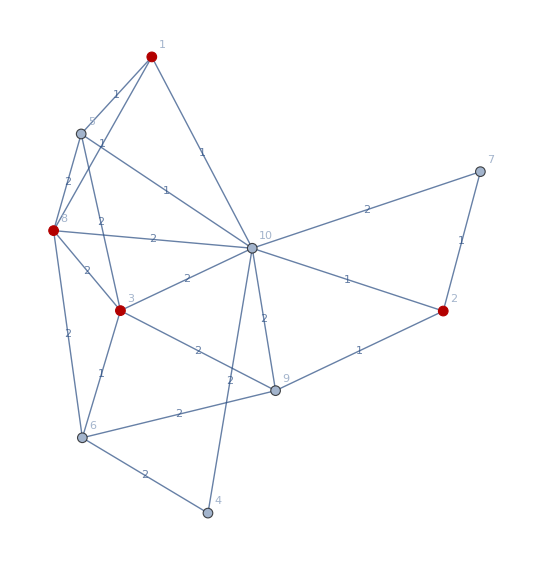

```mathematica
HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]]
```

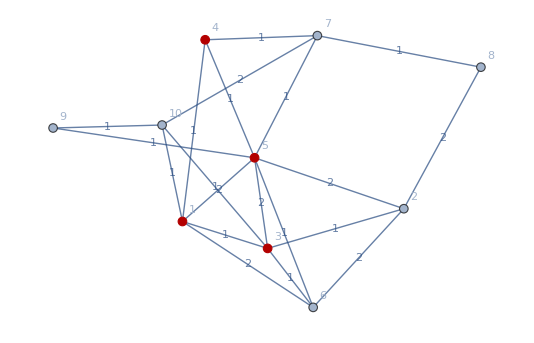
```mathematica
EdgeAdd[-Graphics-,{1<->5,3<->4}]
```

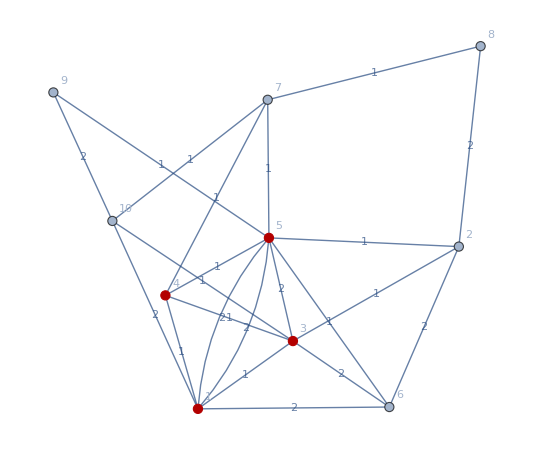

```mathematica
EulerianGraphQ[EdgeAdd[-Graphics-,{1<->3,4<->5}]]
```

True

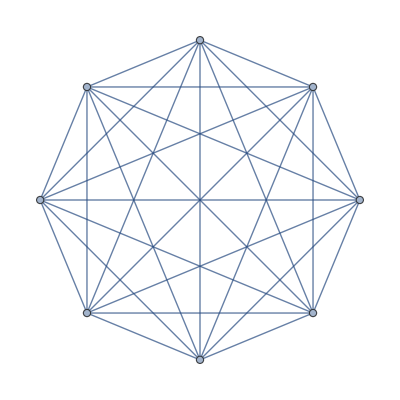

```mathematica
CompleteGraph[8]
```

```mathematica
GraphSum[CompleteGraph[8],CompleteGraph[8]]
```

-Graphics-

```mathematica
EulerianGraphQ[GraphSum[CompleteGraph[8],CompleteGraph[8]]]
```

True

## Function

```mathematica
WeightedAdjacencyMatrix[randomGraph]
```

SparseArray[…]

```mathematica
AssociationThread[Range[4]->VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]]
```

<|1→1,2→3,3→4,4→5|>

```mathematica
Lookup[AssociationThread[Range[4]->VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]],#]&/@{4,2}
```

{5,3}

```mathematica
Lookup[AssociationThread[Range[4]->VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]],#]&/@{1,3}
```

{1,4}

```mathematica
WeightedAdjacencyMatrix[Subgraph[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]]//MatrixForm
```

(0 | 1 | 1 | 2
1 | 0 | 0 | 2
1 | 0 | 0 | 1
2 | 2 | 1 | 0)

```mathematica
MatrixPower[WeightedAdjacencyMatrix[Subgraph[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]],2]//MatrixForm
```

(6 | 4 | 2 | 3
4 | 5 | 3 | 2
2 | 3 | 2 | 2
3 | 2 | 2 | 9)

```mathematica
WeightedAdjacencyMatrix[Subgraph[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]].WeightedAdjacencyMatrix[Subgraph[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]]==MatrixPower[WeightedAdjacencyMatrix[Subgraph[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]],2]
```

True

```mathematica
({{a, b}, {c, d}})^2//MatrixForm
```

(a^2 | b^2
c^2 | d^2)

```mathematica
MatrixPower[({{a, b}, {c, d}}),2]//MatrixForm
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

## Sets and combinations and subsets and permutations and tuples

```mathematica
Array[Indexed[x,#]&,8]
```

{x1,x2,x3,x4,x5,x6,x7,x8}

```mathematica
(100!)/(2*2^50)
```

41445165274797869462064187676138749201511387927068961842188771835900951142952448873009824826210819941897910610263277568000000000000000000000000

```mathematica
(20!)/2^10
```

2375880867360000

```mathematica
(22!)/2^11
```

548828480360160000

```mathematica
(8!)/(2^4 4!)//N
```

105.

```mathematica
(100!)/(2^50 50!)
```

2725392139750729502980713245400918633290796330545803413734328823443106201171875

```mathematica
(20!)/(2^10 10!)
```

654729075

```mathematica
2520/105
```

24

```mathematica
(3!)/(2^3 3!)
```

1/8

```mathematica
Length[Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,#]&,8]]]]]
```

105

```mathematica
Length@Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,#]&,6]]]]
```

15

```mathematica
Table[{(k!)/(2^(k/2)(k/2)!),Length@Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,#]&,k]]]]},{k,{2,4,6,8,10}}]
```

$Aborted

```mathematica
Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,#]&,8]]]]
```

{{{x1,x2},{x3,x4},{x5,x6},{x7,x8}},{{x1,x2},{x3,x4},{x5,x7},{x6,x8}},{{x1,x2},{x3,x4},{x5,x8},{x6,x7}},{{x1,x2},{x3,x5},{x4,x6},{x7,x8}},{{x1,x2},{x3,x5},{x4,x7},{x6,x8}},{{x1,x2},{x3,x5},{x4,x8},{x6,x7}},{{x1,x2},{x3,x6},{x4,x5},{x7,x8}},{{x1,x2},{x3,x6},{x4,x7},{x5,x8}},{{x1,x2},{x3,x6},{x4,x8},{x5,x7}},{{x1,x2},{x3,x7},{x4,x5},{x6,x8}},{{x1,x2},{x3,x7},{x4,x6},{x5,x8}},{{x1,x2},{x3,x7},{x4,x8},{x5,x6}},{{x1,x2},{x3,x8},{x4,x5},{x6,x7}},{{x1,x2},{x3,x8},{x4,x6},{x5,x7}},{{x1,x2},{x3,x8},{x4,x7},{x5,x6}},{{x1,x3},{x2,x4},{x5,x6},{x7,x8}},{{x1,x3},{x2,x4},{x5,x7},{x6,x8}},{{x1,x3},{x2,x4},{x5,x8},{x6,x7}},{{x1,x3},{x2,x5},{x4,x6},{x7,x8}},{{x1,x3},{x2,x5},{x4,x7},{x6,x8}},{{x1,x3},{x2,x5},{x4,x8},{x6,x7}},{{x1,x3},{x2,x6},{x4,x5},{x7,x8}},{{x1,x3},{x2,x6},{x4,x7},{x5,x8}},{{x1,x3},{x2,x6},{x4,x8},{x5,x7}},{{x1,x3},{x2,x7},{x4,x5},{x6,x8}},{{x1,x3},{x2,x7},{x4,x6},{x5,x8}},{{x1,x3},{x2,x7},{x4,x8},{x5,x6}},{{x1,x3},{x2,x8},{x4,x5},{x6,x7}},{{x1,x3},{x2,x8},{x4,x6},{x5,x7}},{{x1,x3},{x2,x8},{x4,x7},{x5,x6}},{{x1,x4},{x2,x3},{x5,x6},{x7,x8}},{{x1,x4},{x2,x3},{x5,x7},{x6,x8}},{{x1,x4},{x2,x3},{x5,x8},{x6,x7}},{{x1,x4},{x2,x5},{x3,x6},{x7,x8}},{{x1,x4},{x2,x5},{x3,x7},{x6,x8}},{{x1,x4},{x2,x5},{x3,x8},{x6,x7}},{{x1,x4},{x2,x6},{x3,x5},{x7,x8}},{{x1,x4},{x2,x6},{x3,x7},{x5,x8}},{{x1,x4},{x2,x6},{x3,x8},{x5,x7}},{{x1,x4},{x2,x7},{x3,x5},{x6,x8}},{{x1,x4},{x2,x7},{x3,x6},{x5,x8}},{{x1,x4},{x2,x7},{x3,x8},{x5,x6}},{{x1,x4},{x2,x8},{x3,x5},{x6,x7}},{{x1,x4},{x2,x8},{x3,x6},{x5,x7}},{{x1,x4},{x2,x8},{x3,x7},{x5,x6}},{{x1,x5},{x2,x3},{x4,x6},{x7,x8}},{{x1,x5},{x2,x3},{x4,x7},{x6,x8}},{{x1,x5},{x2,x3},{x4,x8},{x6,x7}},{{x1,x5},{x2,x4},{x3,x6},{x7,x8}},{{x1,x5},{x2,x4},{x3,x7},{x6,x8}},{{x1,x5},{x2,x4},{x3,x8},{x6,x7}},{{x1,x5},{x2,x6},{x3,x4},{x7,x8}},{{x1,x5},{x2,x6},{x3,x7},{x4,x8}},{{x1,x5},{x2,x6},{x3,x8},{x4,x7}},{{x1,x5},{x2,x7},{x3,x4},{x6,x8}},{{x1,x5},{x2,x7},{x3,x6},{x4,x8}},{{x1,x5},{x2,x7},{x3,x8},{x4,x6}},{{x1,x5},{x2,x8},{x3,x4},{x6,x7}},{{x1,x5},{x2,x8},{x3,x6},{x4,x7}},{{x1,x5},{x2,x8},{x3,x7},{x4,x6}},{{x1,x6},{x2,x3},{x4,x5},{x7,x8}},{{x1,x6},{x2,x3},{x4,x7},{x5,x8}},{{x1,x6},{x2,x3},{x4,x8},{x5,x7}},{{x1,x6},{x2,x4},{x3,x5},{x7,x8}},{{x1,x6},{x2,x4},{x3,x7},{x5,x8}},{{x1,x6},{x2,x4},{x3,x8},{x5,x7}},{{x1,x6},{x2,x5},{x3,x4},{x7,x8}},{{x1,x6},{x2,x5},{x3,x7},{x4,x8}},{{x1,x6},{x2,x5},{x3,x8},{x4,x7}},{{x1,x6},{x2,x7},{x3,x4},{x5,x8}},{{x1,x6},{x2,x7},{x3,x5},{x4,x8}},{{x1,x6},{x2,x7},{x3,x8},{x4,x5}},{{x1,x6},{x2,x8},{x3,x4},{x5,x7}},{{x1,x6},{x2,x8},{x3,x5},{x4,x7}},{{x1,x6},{x2,x8},{x3,x7},{x4,x5}},{{x1,x7},{x2,x3},{x4,x5},{x6,x8}},{{x1,x7},{x2,x3},{x4,x6},{x5,x8}},{{x1,x7},{x2,x3},{x4,x8},{x5,x6}},{{x1,x7},{x2,x4},{x3,x5},{x6,x8}},{{x1,x7},{x2,x4},{x3,x6},{x5,x8}},{{x1,x7},{x2,x4},{x3,x8},{x5,x6}},{{x1,x7},{x2,x5},{x3,x4},{x6,x8}},{{x1,x7},{x2,x5},{x3,x6},{x4,x8}},{{x1,x7},{x2,x5},{x3,x8},{x4,x6}},{{x1,x7},{x2,x6},{x3,x4},{x5,x8}},{{x1,x7},{x2,x6},{x3,x5},{x4,x8}},{{x1,x7},{x2,x6},{x3,x8},{x4,x5}},{{x1,x7},{x2,x8},{x3,x4},{x5,x6}},{{x1,x7},{x2,x8},{x3,x5},{x4,x6}},{{x1,x7},{x2,x8},{x3,x6},{x4,x5}},{{x1,x8},{x2,x3},{x4,x5},{x6,x7}},{{x1,x8},{x2,x3},{x4,x6},{x5,x7}},{{x1,x8},{x2,x3},{x4,x7},{x5,x6}},{{x1,x8},{x2,x4},{x3,x5},{x6,x7}},{{x1,x8},{x2,x4},{x3,x6},{x5,x7}},{{x1,x8},{x2,x4},{x3,x7},{x5,x6}},{{x1,x8},{x2,x5},{x3,x4},{x6,x7}},{{x1,x8},{x2,x5},{x3,x6},{x4,x7}},{{x1,x8},{x2,x5},{x3,x7},{x4,x6}},{{x1,x8},{x2,x6},{x3,x4},{x5,x7}},{{x1,x8},{x2,x6},{x3,x5},{x4,x7}},{{x1,x8},{x2,x6},{x3,x7},{x4,x5}},{{x1,x8},{x2,x7},{x3,x4},{x5,x6}},{{x1,x8},{x2,x7},{x3,x5},{x4,x6}},{{x1,x8},{x2,x7},{x3,x6},{x4,x5}}}

```mathematica
Partition[Array[Indexed[x,#]&,8],4]
```

{{x1,x2,x3,x4},{x5,x6,x7,x8}}

```mathematica
Partition[Array[Indexed[x,#]&,8],2]
```

{{x1,x2},{x3,x4},{x5,x6},{x7,x8}}

```mathematica
Union[Sort/@Union[Sort/@Partition[#,2]&/@Permutations[Array[Indexed[x,#]&,21]]]]
```

Permutations::fac: In Permutations[{x,x,x,x,x,x,x,x,x,x,«11»}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

$Aborted

```mathematica
21!
```

51090942171709440000

## Graph Algorithm

```mathematica
Array[Indexed[x,#]&,10]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}

```mathematica
IncidenceMatrix[randomGraph]
```

SparseArray[…]

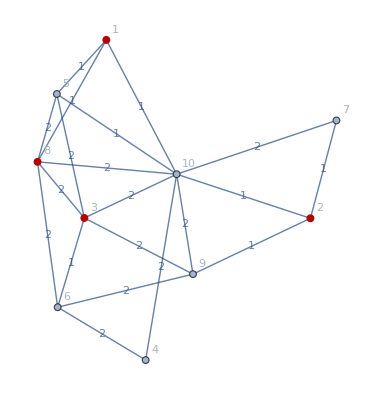

```mathematica
HighlightGraph[randomGraph,VertexList[randomGraph,x_/;OddQ[VertexDegree[randomGraph,x]]]]
```

```mathematica
IncidenceMatrix[randomGraph].Array[Indexed[x,#]&,20]//MatrixForm
```

(x1+x2+x3
x4+x5+x6
x7+x8+x9+x10+x11
x12+x13
x1+x7+x14+x15
x8+x12+x16+x17
x4+x18
x2+x9+x14+x16+x19
x5+x10+x17+x20
x3+x6+x11+x13+x15+x18+x19+x20)

```mathematica
AnnotationValue[randomGraph,EdgeWeight]
```

{1,1,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,2,2,2}

```mathematica
Length[{1,1,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,2,2,2}]
```

20

```mathematica
Length[IncidenceMatrix[randomGraph].Array[Indexed[x,#]&,20]]
```

10

```mathematica
{1,1,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,2,2,2}.IncidenceMatrix[randomGraph]ᵀ
```

{3,3,9,4,6,7,3,9,7,13}

```mathematica
IncidenceMatrix[randomGraph]ᵀ.({1,1,1,1,1,1,2,1,2,2,2,2,2,2,1,2,2,2,2,2}.Array[Indexed[x,#]&,20])
```

SparseArray[…].(x1+x2+x3+x4+x5+x6+2 x7+x8+2 x9+2 x10+2 x11+2 x12+2 x13+2 x14+x15+2 x16+2 x17+2 x18+2 x19+2 x20)

```mathematica
IncidenceMatrix[randomGraph]//MatrixForm
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1)

```mathematica
Transpose[IncidenceMatrix[randomGraph]]//MatrixForm
```

(1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

```mathematica
RandomInteger[{1,2},10].IncidenceMatrix[randomGraph]//MatrixForm
```

(3
3
4
4
3
4
2
3
2
2
3
4
4
2
3
3
3
4
3
3)

```mathematica
Array[Indexed[x,#]&,20]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}

```mathematica
Array[Indexed[x,#]&,20].AnnotationValue[randomGraph,EdgeWeight]
```

x1+x2+x3+x4+x5+x6+2 x7+x8+2 x9+2 x10+2 x11+2 x12+2 x13+2 x14+x15+2 x16+2 x17+2 x18+2 x19+2 x20

```mathematica
(set↦TrueQ[OddQ[Count[set_,x_/;OddQ[VertexDegree[randomGraph,x]]]]])[{1,2,3,4,5}]
```

False

```mathematica
EdgeList@Subgraph[randomGraph,{1,2,3,4,5}]
```

{1<->5,3<->5}

```mathematica
Total[Table[Indexed[x,k],{k,EdgeIndex[randomGraph,EdgeList@Subgraph[randomGraph,#]]}]]&/@Select[Subsets[VertexList[randomGraph]],(set↦TrueQ[OddQ[Count[set_,x_/;OddQ[VertexDegree[randomGraph,x]]]]])]
```

{}

```mathematica
Select[Subsets[VertexList[randomGraph]],OddQ[Count[#,x_/;OddQ[VertexDegree[randomGraph,x]]]]==True&]
```

{{1},{2},{3},{8},{1,4},{1,5},{1,6},{1,7},{1,9},{1,10},{2,4},{2,5},{2,6},{2,7},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,9},{3,10},{4,8},{5,8},{6,8},{7,8},{8,9},{8,10},{1,2,3},{1,2,8},{1,3,8},{1,4,5},{1,4,6},{1,4,7},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,9},{1,5,10},{1,6,7},{1,6,9},{1,6,10},{1,7,9},{1,7,10},{1,9,10},{2,3,8},{2,4,5},{2,4,6},{2,4,7},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,9},{2,5,10},{2,6,7},{2,6,9},{2,6,10},{2,7,9},{2,7,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,9},{3,5,10},{3,6,7},{3,6,9},{3,6,10},{3,7,9},{3,7,10},{3,9,10},{4,5,8},{4,6,8},{4,7,8},{4,8,9},{4,8,10},{5,6,8},{5,7,8},{5,8,9},{5,8,10},{6,7,8},{6,8,9},{6,8,10},{7,8,9},{7,8,10},{8,9,10},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,9},{1,2,3,10},{1,2,4,8},{1,2,5,8},{1,2,6,8},{1,2,7,8},{1,2,8,9},{1,2,8,10},{1,3,4,8},{1,3,5,8},{1,3,6,8},{1,3,7,8},{1,3,8,9},{1,3,8,10},{1,4,5,6},{1,4,5,7},{1,4,5,9},{1,4,5,10},{1,4,6,7},{1,4,6,9},{1,4,6,10},{1,4,7,9},{1,4,7,10},{1,4,9,10},{1,5,6,7},{1,5,6,9},{1,5,6,10},{1,5,7,9},{1,5,7,10},{1,5,9,10},{1,6,7,9},{1,6,7,10},{1,6,9,10},{1,7,9,10},{2,3,4,8},{2,3,5,8},{2,3,6,8},{2,3,7,8},{2,3,8,9},{2,3,8,10},{2,4,5,6},{2,4,5,7},{2,4,5,9},{2,4,5,10},{2,4,6,7},{2,4,6,9},{2,4,6,10},{2,4,7,9},{2,4,7,10},{2,4,9,10},{2,5,6,7},{2,5,6,9},{2,5,6,10},{2,5,7,9},{2,5,7,10},{2,5,9,10},{2,6,7,9},{2,6,7,10},{2,6,9,10},{2,7,9,10},{3,4,5,6},{3,4,5,7},{3,4,5,9},{3,4,5,10},{3,4,6,7},{3,4,6,9},{3,4,6,10},{3,4,7,9},{3,4,7,10},{3,4,9,10},{3,5,6,7},{3,5,6,9},{3,5,6,10},{3,5,7,9},{3,5,7,10},{3,5,9,10},{3,6,7,9},{3,6,7,10},{3,6,9,10},{3,7,9,10},{4,5,6,8},{4,5,7,8},{4,5,8,9},{4,5,8,10},{4,6,7,8},{4,6,8,9},{4,6,8,10},{4,7,8,9},{4,7,8,10},{4,8,9,10},{5,6,7,8},{5,6,8,9},{5,6,8,10},{5,7,8,9},{5,7,8,10},{5,8,9,10},{6,7,8,9},{6,7,8,10},{6,8,9,10},{7,8,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,9,10},{1,2,4,5,8},{1,2,4,6,8},{1,2,4,7,8},{1,2,4,8,9},{1,2,4,8,10},{1,2,5,6,8},{1,2,5,7,8},{1,2,5,8,9},{1,2,5,8,10},{1,2,6,7,8},{1,2,6,8,9},{1,2,6,8,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,8,9,10},{1,3,4,5,8},{1,3,4,6,8},{1,3,4,7,8},{1,3,4,8,9},{1,3,4,8,10},{1,3,5,6,8},{1,3,5,7,8},{1,3,5,8,9},{1,3,5,8,10},{1,3,6,7,8},{1,3,6,8,9},{1,3,6,8,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,9,10},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,9,10},{1,4,7,9,10},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,9,10},{1,5,7,9,10},{1,6,7,9,10},{2,3,4,5,8},{2,3,4,6,8},{2,3,4,7,8},{2,3,4,8,9},{2,3,4,8,10},{2,3,5,6,8},{2,3,5,7,8},{2,3,5,8,9},{2,3,5,8,10},{2,3,6,7,8},{2,3,6,8,9},{2,3,6,8,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,9,10},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,9,10},{2,4,7,9,10},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,9,10},{2,5,7,9,10},{2,6,7,9,10},{3,4,5,6,7},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,9,10},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,9,10},{3,4,7,9,10},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,9,10},{3,5,7,9,10},{3,6,7,9,10},{4,5,6,7,8},{4,5,6,8,9},{4,5,6,8,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,9},{1,2,3,4,7,10},{1,2,3,4,9,10},{1,2,3,5,6,7},{1,2,3,5,6,9},{1,2,3,5,6,10},{1,2,3,5,7,9},{1,2,3,5,7,10},{1,2,3,5,9,10},{1,2,3,6,7,9},{1,2,3,6,7,10},{1,2,3,6,9,10},{1,2,3,7,9,10},{1,2,4,5,6,8},{1,2,4,5,7,8},{1,2,4,5,8,9},{1,2,4,5,8,10},{1,2,4,6,7,8},{1,2,4,6,8,9},{1,2,4,6,8,10},{1,2,4,7,8,9},{1,2,4,7,8,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,8,9},{1,2,5,6,8,10},{1,2,5,7,8,9},{1,2,5,7,8,10},{1,2,5,8,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,8,9,10},{1,2,7,8,9,10},{1,3,4,5,6,8},{1,3,4,5,7,8},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,6,7,8},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,7,8,9},{1,3,4,7,8,10},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,8,9,10},{1,3,7,8,9,10},{1,4,5,6,7,9},{1,4,5,6,7,10},{1,4,5,6,9,10},{1,4,5,7,9,10},{1,4,6,7,9,10},{1,5,6,7,9,10},{2,3,4,5,6,8},{2,3,4,5,7,8},{2,3,4,5,8,9},{2,3,4,5,8,10},{2,3,4,6,7,8},{2,3,4,6,8,9},{2,3,4,6,8,10},{2,3,4,7,8,9},{2,3,4,7,8,10},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,8,9},{2,3,5,6,8,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,6,8,9,10},{2,3,7,8,9,10},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,9,10},{2,4,5,7,9,10},{2,4,6,7,9,10},{2,5,6,7,9,10},{3,4,5,6,7,9},{3,4,5,6,7,10},{3,4,5,6,9,10},{3,4,5,7,9,10},{3,4,6,7,9,10},{3,5,6,7,9,10},{4,5,6,7,8,9},{4,5,6,7,8,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,9,10},{1,2,3,4,7,9,10},{1,2,3,5,6,7,9},{1,2,3,5,6,7,10},{1,2,3,5,6,9,10},{1,2,3,5,7,9,10},{1,2,3,6,7,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,9,10},{3,4,5,6,7,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,9,10},{1,2,3,4,6,7,9,10},{1,2,3,5,6,7,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{1,2,3,4,5,6,7,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10}}

```mathematica
Total[Table[Indexed[x,k],{k,EdgeIndex[randomGraph,EdgeList@Subgraph[randomGraph,#]]}]]&/@Select[Subsets[VertexList[randomGraph]],OddQ[Count[#,x_/;OddQ[VertexDegree[randomGraph,x]]]]==True&]\[VectorGreaterEqual]ConstantArray[1,Length[Select[Subsets[VertexList[randomGraph]],OddQ[Count[#,x_/;OddQ[VertexDegree[randomGraph,x]]]]==True&]]]
```

{0,0,0,0,0,x1,0,0,0,x3,0,0,0,x4,x5,x6,0,x7,x8,0,x10,x11,0,x14,x16,0,0,x19,0,x2,x2+x9,x1,x12,0,0,x3+x13,x1,x1,x1,x1+x3+x15,0,x17,x3,0,x3+x18,x3+x20,x9,0,x12,x4,x5,x6+x13,0,x4,x5,x6+x15,x4,x5+x17,x6,x4+x5,x4+x6+x18,x5+x6+x20,x7,x8+x12,0,x10,x11+x13,x7+x8,x7,x7+x10,x7+x11+x15,x8,x8+x10+x17,x8+x11,x10,x11+x18,x10+x11+x20,x14,x12+x16,0,0,x13+x19,x14+x16,x14,x14,x14+x15+x19,x16,x16+x17,x16+x19,0,x18+x19,x19+x20,0,x1+x7,x8,x4,x5+x10,x3+x6+x11,x2,x1+x2+x14,x2+x16,x2+x4,x2+x5,x2+x3+x6+x19,x2+x9,x1+x2+x7+x9+x14,x2+x8+x9+x16,x2+x9,x2+x9+x10,x2+x3+x9+x11+x19,x1+x12,x1,x1,x1+x3+x13+x15,x12,x12+x17,x3+x12+x13,0,x3+x13+x18,x3+x13+x20,x1,x1+x17,x1+x3+x15,x1,x1+x3+x15+x18,x1+x3+x15+x20,x17,x3+x18,x3+x17+x20,x3+x18+x20,x9,x7+x9+x14,x8+x9+x16,x4+x9,x5+x9+x10,x6+x9+x11+x19,x12,x4,x5,x6+x13+x15,x4+x12,x5+x12+x17,x6+x12+x13,x4+x5,x4+x6+x13+x18,x5+x6+x13+x20,x4,x5+x17,x6+x15,x4+x5,x4+x6+x15+x18,x5+x6+x15+x20,x4+x5+x17,x4+x6+x18,x5+x6+x17+x20,x4+x5+x6+x18+x20,x7+x8+x12,x7,x7+x10,x7+x11+x13+x15,x8+x12,x8+x10+x12+x17,x8+x11+x12+x13,x10,x11+x13+x18,x10+x11+x13+x20,x7+x8,x7+x8+x10+x17,x7+x8+x11+x15,x7+x10,x7+x11+x15+x18,x7+x10+x11+x15+x20,x8+x10+x17,x8+x11+x18,x8+x10+x11+x17+x20,x10+x11+x18+x20,x12+x14+x16,x14,x14,x13+x14+x15+x19,x12+x16,x12+x16+x17,x12+x13+x16+x19,0,x13+x18+x19,x13+x19+x20,x14+x16,x14+x16+x17,x14+x15+x16+x19,x14,x14+x15+x18+x19,x14+x15+x19+x20,x16+x17,x16+x18+x19,x16+x17+x19+x20,x18+x19+x20,x1+x7,x8+x12,x4,x5+x10,x3+x6+x11+x13,x1+x7+x8,x1+x4+x7,x1+x5+x7+x10,x1+x3+x6+x7+x11+x15,x4+x8,x5+x8+x10+x17,x3+x6+x8+x11,x4+x5+x10,x3+x4+x6+x11+x18,x3+x5+x6+x10+x11+x20,x1+x2+x14,x2+x12+x16,x2+x4,x2+x5,x2+x3+x6+x13+x19,x1+x2+x14+x16,x1+x2+x4+x14,x1+x2+x5+x14,x1+x2+x3+x6+x14+x15+x19,x2+x4+x16,x2+x5+x16+x17,x2+x3+x6+x16+x19,x2+x4+x5,x2+x3+x4+x6+x18+x19,x2+x3+x5+x6+x19+x20,x1+x2+x7+x9+x14,x2+x8+x9+x12+x16,x2+x9,x2+x9+x10,x2+x3+x9+x11+x13+x19,x1+x2+x7+x8+x9+x14+x16,x1+x2+x7+x9+x14,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x14+x15+x19,x2+x8+x9+x16,x2+x8+x9+x10+x16+x17,x2+x3+x8+x9+x11+x16+x19,x2+x9+x10,x2+x3+x9+x11+x18+x19,x2+x3+x9+x10+x11+x19+x20,x1+x12,x1+x12+x17,x1+x3+x12+x13+x15,x1,x1+x3+x13+x15+x18,x1+x3+x13+x15+x20,x12+x17,x3+x12+x13+x18,x3+x12+x13+x17+x20,x3+x13+x18+x20,x1+x17,x1+x3+x15+x18,x1+x3+x15+x17+x20,x1+x3+x15+x18+x20,x3+x17+x18+x20,x7+x9+x14,x8+x9+x12+x16,x4+x9,x5+x9+x10,x6+x9+x11+x13+x19,x7+x8+x9+x14+x16,x4+x7+x9+x14,x5+x7+x9+x10+x14,x6+x7+x9+x11+x14+x15+x19,x4+x8+x9+x16,x5+x8+x9+x10+x16+x17,x6+x8+x9+x11+x16+x19,x4+x5+x9+x10,x4+x6+x9+x11+x18+x19,x5+x6+x9+x10+x11+x19+x20,x4+x12,x5+x12+x17,x6+x12+x13+x15,x4+x5,x4+x6+x13+x15+x18,x5+x6+x13+x15+x20,x4+x5+x12+x17,x4+x6+x12+x13+x18,x5+x6+x12+x13+x17+x20,x4+x5+x6+x13+x18+x20,x4+x5+x17,x4+x6+x15+x18,x5+x6+x15+x17+x20,x4+x5+x6+x15+x18+x20,x4+x5+x6+x17+x18+x20,x7+x8+x12,x7+x8+x10+x12+x17,x7+x8+x11+x12+x13+x15,x7+x10,x7+x11+x13+x15+x18,x7+x10+x11+x13+x15+x20,x8+x10+x12+x17,x8+x11+x12+x13+x18,x8+x10+x11+x12+x13+x17+x20,x10+x11+x13+x18+x20,x7+x8+x10+x17,x7+x8+x11+x15+x18,x7+x8+x10+x11+x15+x17+x20,x7+x10+x11+x15+x18+x20,x8+x10+x11+x17+x18+x20,x12+x14+x16,x12+x14+x16+x17,x12+x13+x14+x15+x16+x19,x14,x13+x14+x15+x18+x19,x13+x14+x15+x19+x20,x12+x16+x17,x12+x13+x16+x18+x19,x12+x13+x16+x17+x19+x20,x13+x18+x19+x20,x14+x16+x17,x14+x15+x16+x18+x19,x14+x15+x16+x17+x19+x20,x14+x15+x18+x19+x20,x16+x17+x18+x19+x20,x1+x7+x8+x12,x1+x4+x7,x1+x5+x7+x10,x1+x3+x6+x7+x11+x13+x15,x4+x8+x12,x5+x8+x10+x12+x17,x3+x6+x8+x11+x12+x13,x4+x5+x10,x3+x4+x6+x11+x13+x18,x3+x5+x6+x10+x11+x13+x20,x1+x4+x7+x8,x1+x5+x7+x8+x10+x17,x1+x3+x6+x7+x8+x11+x15,x1+x4+x5+x7+x10,x1+x3+x4+x6+x7+x11+x15+x18,x1+x3+x5+x6+x7+x10+x11+x15+x20,x4+x5+x8+x10+x17,x3+x4+x6+x8+x11+x18,x3+x5+x6+x8+x10+x11+x17+x20,x3+x4+x5+x6+x10+x11+x18+x20,x1+x2+x12+x14+x16,x1+x2+x4+x14,x1+x2+x5+x14,x1+x2+x3+x6+x13+x14+x15+x19,x2+x4+x12+x16,x2+x5+x12+x16+x17,x2+x3+x6+x12+x13+x16+x19,x2+x4+x5,x2+x3+x4+x6+x13+x18+x19,x2+x3+x5+x6+x13+x19+x20,x1+x2+x4+x14+x16,x1+x2+x5+x14+x16+x17,x1+x2+x3+x6+x14+x15+x16+x19,x1+x2+x4+x5+x14,x1+x2+x3+x4+x6+x14+x15+x18+x19,x1+x2+x3+x5+x6+x14+x15+x19+x20,x2+x4+x5+x16+x17,x2+x3+x4+x6+x16+x18+x19,x2+x3+x5+x6+x16+x17+x19+x20,x2+x3+x4+x5+x6+x18+x19+x20,x1+x2+x7+x8+x9+x12+x14+x16,x1+x2+x7+x9+x14,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x13+x14+x15+x19,x2+x8+x9+x12+x16,x2+x8+x9+x10+x12+x16+x17,x2+x3+x8+x9+x11+x12+x13+x16+x19,x2+x9+x10,x2+x3+x9+x11+x13+x18+x19,x2+x3+x9+x10+x11+x13+x19+x20,x1+x2+x7+x8+x9+x14+x16,x1+x2+x7+x8+x9+x10+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x14+x15+x16+x19,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x14+x15+x18+x19,x1+x2+x3+x7+x9+x10+x11+x14+x15+x19+x20,x2+x8+x9+x10+x16+x17,x2+x3+x8+x9+x11+x16+x18+x19,x2+x3+x8+x9+x10+x11+x16+x17+x19+x20,x2+x3+x9+x10+x11+x18+x19+x20,x1+x12+x17,x1+x3+x12+x13+x15+x18,x1+x3+x12+x13+x15+x17+x20,x1+x3+x13+x15+x18+x20,x3+x12+x13+x17+x18+x20,x1+x3+x15+x17+x18+x20,x7+x8+x9+x12+x14+x16,x4+x7+x9+x14,x5+x7+x9+x10+x14,x6+x7+x9+x11+x13+x14+x15+x19,x4+x8+x9+x12+x16,x5+x8+x9+x10+x12+x16+x17,x6+x8+x9+x11+x12+x13+x16+x19,x4+x5+x9+x10,x4+x6+x9+x11+x13+x18+x19,x5+x6+x9+x10+x11+x13+x19+x20,x4+x7+x8+x9+x14+x16,x5+x7+x8+x9+x10+x14+x16+x17,x6+x7+x8+x9+x11+x14+x15+x16+x19,x4+x5+x7+x9+x10+x14,x4+x6+x7+x9+x11+x14+x15+x18+x19,x5+x6+x7+x9+x10+x11+x14+x15+x19+x20,x4+x5+x8+x9+x10+x16+x17,x4+x6+x8+x9+x11+x16+x18+x19,x5+x6+x8+x9+x10+x11+x16+x17+x19+x20,x4+x5+x6+x9+x10+x11+x18+x19+x20,x4+x5+x12+x17,x4+x6+x12+x13+x15+x18,x5+x6+x12+x13+x15+x17+x20,x4+x5+x6+x13+x15+x18+x20,x4+x5+x6+x12+x13+x17+x18+x20,x4+x5+x6+x15+x17+x18+x20,x7+x8+x10+x12+x17,x7+x8+x11+x12+x13+x15+x18,x7+x8+x10+x11+x12+x13+x15+x17+x20,x7+x10+x11+x13+x15+x18+x20,x8+x10+x11+x12+x13+x17+x18+x20,x7+x8+x10+x11+x15+x17+x18+x20,x12+x14+x16+x17,x12+x13+x14+x15+x16+x18+x19,x12+x13+x14+x15+x16+x17+x19+x20,x13+x14+x15+x18+x19+x20,x12+x13+x16+x17+x18+x19+x20,x14+x15+x16+x17+x18+x19+x20,x1+x4+x7+x8+x12,x1+x5+x7+x8+x10+x12+x17,x1+x3+x6+x7+x8+x11+x12+x13+x15,x1+x4+x5+x7+x10,x1+x3+x4+x6+x7+x11+x13+x15+x18,x1+x3+x5+x6+x7+x10+x11+x13+x15+x20,x4+x5+x8+x10+x12+x17,x3+x4+x6+x8+x11+x12+x13+x18,x3+x5+x6+x8+x10+x11+x12+x13+x17+x20,x3+x4+x5+x6+x10+x11+x13+x18+x20,x1+x4+x5+x7+x8+x10+x17,x1+x3+x4+x6+x7+x8+x11+x15+x18,x1+x3+x5+x6+x7+x8+x10+x11+x15+x17+x20,x1+x3+x4+x5+x6+x7+x10+x11+x15+x18+x20,x3+x4+x5+x6+x8+x10+x11+x17+x18+x20,x1+x2+x4+x12+x14+x16,x1+x2+x5+x12+x14+x16+x17,x1+x2+x3+x6+x12+x13+x14+x15+x16+x19,x1+x2+x4+x5+x14,x1+x2+x3+x4+x6+x13+x14+x15+x18+x19,x1+x2+x3+x5+x6+x13+x14+x15+x19+x20,x2+x4+x5+x12+x16+x17,x2+x3+x4+x6+x12+x13+x16+x18+x19,x2+x3+x5+x6+x12+x13+x16+x17+x19+x20,x2+x3+x4+x5+x6+x13+x18+x19+x20,x1+x2+x4+x5+x14+x16+x17,x1+x2+x3+x4+x6+x14+x15+x16+x18+x19,x1+x2+x3+x5+x6+x14+x15+x16+x17+x19+x20,x1+x2+x3+x4+x5+x6+x14+x15+x18+x19+x20,x2+x3+x4+x5+x6+x16+x17+x18+x19+x20,x1+x2+x7+x8+x9+x12+x14+x16,x1+x2+x7+x8+x9+x10+x12+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x12+x13+x14+x15+x16+x19,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x13+x14+x15+x18+x19,x1+x2+x3+x7+x9+x10+x11+x13+x14+x15+x19+x20,x2+x8+x9+x10+x12+x16+x17,x2+x3+x8+x9+x11+x12+x13+x16+x18+x19,x2+x3+x8+x9+x10+x11+x12+x13+x16+x17+x19+x20,x2+x3+x9+x10+x11+x13+x18+x19+x20,x1+x2+x7+x8+x9+x10+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x14+x15+x16+x18+x19,x1+x2+x3+x7+x8+x9+x10+x11+x14+x15+x16+x17+x19+x20,x1+x2+x3+x7+x9+x10+x11+x14+x15+x18+x19+x20,x2+x3+x8+x9+x10+x11+x16+x17+x18+x19+x20,x1+x3+x12+x13+x15+x17+x18+x20,x4+x7+x8+x9+x12+x14+x16,x5+x7+x8+x9+x10+x12+x14+x16+x17,x6+x7+x8+x9+x11+x12+x13+x14+x15+x16+x19,x4+x5+x7+x9+x10+x14,x4+x6+x7+x9+x11+x13+x14+x15+x18+x19,x5+x6+x7+x9+x10+x11+x13+x14+x15+x19+x20,x4+x5+x8+x9+x10+x12+x16+x17,x4+x6+x8+x9+x11+x12+x13+x16+x18+x19,x5+x6+x8+x9+x10+x11+x12+x13+x16+x17+x19+x20,x4+x5+x6+x9+x10+x11+x13+x18+x19+x20,x4+x5+x7+x8+x9+x10+x14+x16+x17,x4+x6+x7+x8+x9+x11+x14+x15+x16+x18+x19,x5+x6+x7+x8+x9+x10+x11+x14+x15+x16+x17+x19+x20,x4+x5+x6+x7+x9+x10+x11+x14+x15+x18+x19+x20,x4+x5+x6+x8+x9+x10+x11+x16+x17+x18+x19+x20,x4+x5+x6+x12+x13+x15+x17+x18+x20,x7+x8+x10+x11+x12+x13+x15+x17+x18+x20,x12+x13+x14+x15+x16+x17+x18+x19+x20,x1+x4+x5+x7+x8+x10+x12+x17,x1+x3+x4+x6+x7+x8+x11+x12+x13+x15+x18,x1+x3+x5+x6+x7+x8+x10+x11+x12+x13+x15+x17+x20,x1+x3+x4+x5+x6+x7+x10+x11+x13+x15+x18+x20,x3+x4+x5+x6+x8+x10+x11+x12+x13+x17+x18+x20,x1+x3+x4+x5+x6+x7+x8+x10+x11+x15+x17+x18+x20,x1+x2+x4+x5+x12+x14+x16+x17,x1+x2+x3+x4+x6+x12+x13+x14+x15+x16+x18+x19,x1+x2+x3+x5+x6+x12+x13+x14+x15+x16+x17+x19+x20,x1+x2+x3+x4+x5+x6+x13+x14+x15+x18+x19+x20,x2+x3+x4+x5+x6+x12+x13+x16+x17+x18+x19+x20,x1+x2+x3+x4+x5+x6+x14+x15+x16+x17+x18+x19+x20,x1+x2+x7+x8+x9+x10+x12+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x12+x13+x14+x15+x16+x18+x19,x1+x2+x3+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x19+x20,x1+x2+x3+x7+x9+x10+x11+x13+x14+x15+x18+x19+x20,x2+x3+x8+x9+x10+x11+x12+x13+x16+x17+x18+x19+x20,x1+x2+x3+x7+x8+x9+x10+x11+x14+x15+x16+x17+x18+x19+x20,x4+x5+x7+x8+x9+x10+x12+x14+x16+x17,x4+x6+x7+x8+x9+x11+x12+x13+x14+x15+x16+x18+x19,x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x19+x20,x4+x5+x6+x7+x9+x10+x11+x13+x14+x15+x18+x19+x20,x4+x5+x6+x8+x9+x10+x11+x12+x13+x16+x17+x18+x19+x20,x4+x5+x6+x7+x8+x9+x10+x11+x14+x15+x16+x17+x18+x19+x20,x1+x3+x4+x5+x6+x7+x8+x10+x11+x12+x13+x15+x17+x18+x20,x1+x2+x3+x4+x5+x6+x12+x13+x14+x15+x16+x17+x18+x19+x20,x1+x2+x3+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20,x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20}\[VectorGreaterEqual]{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Subsets[VertexList[randomGraph]]
```

{{},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{5,6},{5,7},{5,8},{5,9},{5,10},{6,7},{6,8},{6,9},{6,10},{7,8},{7,9},{7,10},{8,9},{8,10},{9,10},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8},{1,2,9},{1,2,10},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8},{1,3,9},{1,3,10},{1,4,5},{1,4,6},{1,4,7},{1,4,8},{1,4,9},{1,4,10},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{1,5,10},{1,6,7},{1,6,8},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10},{1,8,9},{1,8,10},{1,9,10},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8},{2,3,9},{2,3,10},{2,4,5},{2,4,6},{2,4,7},{2,4,8},{2,4,9},{2,4,10},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{2,5,10},{2,6,7},{2,6,8},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10},{2,8,9},{2,8,10},{2,9,10},{3,4,5},{3,4,6},{3,4,7},{3,4,8},{3,4,9},{3,4,10},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{3,5,10},{3,6,7},{3,6,8},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10},{3,8,9},{3,8,10},{3,9,10},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{4,5,10},{4,6,7},{4,6,8},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10},{4,8,9},{4,8,10},{4,9,10},{5,6,7},{5,6,8},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10},{5,8,9},{5,8,10},{5,9,10},{6,7,8},{6,7,9},{6,7,10},{6,8,9},{6,8,10},{6,9,10},{7,8,9},{7,8,10},{7,9,10},{8,9,10},{1,2,3,4},{1,2,3,5},{1,2,3,6},{1,2,3,7},{1,2,3,8},{1,2,3,9},{1,2,3,10},{1,2,4,5},{1,2,4,6},{1,2,4,7},{1,2,4,8},{1,2,4,9},{1,2,4,10},{1,2,5,6},{1,2,5,7},{1,2,5,8},{1,2,5,9},{1,2,5,10},{1,2,6,7},{1,2,6,8},{1,2,6,9},{1,2,6,10},{1,2,7,8},{1,2,7,9},{1,2,7,10},{1,2,8,9},{1,2,8,10},{1,2,9,10},{1,3,4,5},{1,3,4,6},{1,3,4,7},{1,3,4,8},{1,3,4,9},{1,3,4,10},{1,3,5,6},{1,3,5,7},{1,3,5,8},{1,3,5,9},{1,3,5,10},{1,3,6,7},{1,3,6,8},{1,3,6,9},{1,3,6,10},{1,3,7,8},{1,3,7,9},{1,3,7,10},{1,3,8,9},{1,3,8,10},{1,3,9,10},{1,4,5,6},{1,4,5,7},{1,4,5,8},{1,4,5,9},{1,4,5,10},{1,4,6,7},{1,4,6,8},{1,4,6,9},{1,4,6,10},{1,4,7,8},{1,4,7,9},{1,4,7,10},{1,4,8,9},{1,4,8,10},{1,4,9,10},{1,5,6,7},{1,5,6,8},{1,5,6,9},{1,5,6,10},{1,5,7,8},{1,5,7,9},{1,5,7,10},{1,5,8,9},{1,5,8,10},{1,5,9,10},{1,6,7,8},{1,6,7,9},{1,6,7,10},{1,6,8,9},{1,6,8,10},{1,6,9,10},{1,7,8,9},{1,7,8,10},{1,7,9,10},{1,8,9,10},{2,3,4,5},{2,3,4,6},{2,3,4,7},{2,3,4,8},{2,3,4,9},{2,3,4,10},{2,3,5,6},{2,3,5,7},{2,3,5,8},{2,3,5,9},{2,3,5,10},{2,3,6,7},{2,3,6,8},{2,3,6,9},{2,3,6,10},{2,3,7,8},{2,3,7,9},{2,3,7,10},{2,3,8,9},{2,3,8,10},{2,3,9,10},{2,4,5,6},{2,4,5,7},{2,4,5,8},{2,4,5,9},{2,4,5,10},{2,4,6,7},{2,4,6,8},{2,4,6,9},{2,4,6,10},{2,4,7,8},{2,4,7,9},{2,4,7,10},{2,4,8,9},{2,4,8,10},{2,4,9,10},{2,5,6,7},{2,5,6,8},{2,5,6,9},{2,5,6,10},{2,5,7,8},{2,5,7,9},{2,5,7,10},{2,5,8,9},{2,5,8,10},{2,5,9,10},{2,6,7,8},{2,6,7,9},{2,6,7,10},{2,6,8,9},{2,6,8,10},{2,6,9,10},{2,7,8,9},{2,7,8,10},{2,7,9,10},{2,8,9,10},{3,4,5,6},{3,4,5,7},{3,4,5,8},{3,4,5,9},{3,4,5,10},{3,4,6,7},{3,4,6,8},{3,4,6,9},{3,4,6,10},{3,4,7,8},{3,4,7,9},{3,4,7,10},{3,4,8,9},{3,4,8,10},{3,4,9,10},{3,5,6,7},{3,5,6,8},{3,5,6,9},{3,5,6,10},{3,5,7,8},{3,5,7,9},{3,5,7,10},{3,5,8,9},{3,5,8,10},{3,5,9,10},{3,6,7,8},{3,6,7,9},{3,6,7,10},{3,6,8,9},{3,6,8,10},{3,6,9,10},{3,7,8,9},{3,7,8,10},{3,7,9,10},{3,8,9,10},{4,5,6,7},{4,5,6,8},{4,5,6,9},{4,5,6,10},{4,5,7,8},{4,5,7,9},{4,5,7,10},{4,5,8,9},{4,5,8,10},{4,5,9,10},{4,6,7,8},{4,6,7,9},{4,6,7,10},{4,6,8,9},{4,6,8,10},{4,6,9,10},{4,7,8,9},{4,7,8,10},{4,7,9,10},{4,8,9,10},{5,6,7,8},{5,6,7,9},{5,6,7,10},{5,6,8,9},{5,6,8,10},{5,6,9,10},{5,7,8,9},{5,7,8,10},{5,7,9,10},{5,8,9,10},{6,7,8,9},{6,7,8,10},{6,7,9,10},{6,8,9,10},{7,8,9,10},{1,2,3,4,5},{1,2,3,4,6},{1,2,3,4,7},{1,2,3,4,8},{1,2,3,4,9},{1,2,3,4,10},{1,2,3,5,6},{1,2,3,5,7},{1,2,3,5,8},{1,2,3,5,9},{1,2,3,5,10},{1,2,3,6,7},{1,2,3,6,8},{1,2,3,6,9},{1,2,3,6,10},{1,2,3,7,8},{1,2,3,7,9},{1,2,3,7,10},{1,2,3,8,9},{1,2,3,8,10},{1,2,3,9,10},{1,2,4,5,6},{1,2,4,5,7},{1,2,4,5,8},{1,2,4,5,9},{1,2,4,5,10},{1,2,4,6,7},{1,2,4,6,8},{1,2,4,6,9},{1,2,4,6,10},{1,2,4,7,8},{1,2,4,7,9},{1,2,4,7,10},{1,2,4,8,9},{1,2,4,8,10},{1,2,4,9,10},{1,2,5,6,7},{1,2,5,6,8},{1,2,5,6,9},{1,2,5,6,10},{1,2,5,7,8},{1,2,5,7,9},{1,2,5,7,10},{1,2,5,8,9},{1,2,5,8,10},{1,2,5,9,10},{1,2,6,7,8},{1,2,6,7,9},{1,2,6,7,10},{1,2,6,8,9},{1,2,6,8,10},{1,2,6,9,10},{1,2,7,8,9},{1,2,7,8,10},{1,2,7,9,10},{1,2,8,9,10},{1,3,4,5,6},{1,3,4,5,7},{1,3,4,5,8},{1,3,4,5,9},{1,3,4,5,10},{1,3,4,6,7},{1,3,4,6,8},{1,3,4,6,9},{1,3,4,6,10},{1,3,4,7,8},{1,3,4,7,9},{1,3,4,7,10},{1,3,4,8,9},{1,3,4,8,10},{1,3,4,9,10},{1,3,5,6,7},{1,3,5,6,8},{1,3,5,6,9},{1,3,5,6,10},{1,3,5,7,8},{1,3,5,7,9},{1,3,5,7,10},{1,3,5,8,9},{1,3,5,8,10},{1,3,5,9,10},{1,3,6,7,8},{1,3,6,7,9},{1,3,6,7,10},{1,3,6,8,9},{1,3,6,8,10},{1,3,6,9,10},{1,3,7,8,9},{1,3,7,8,10},{1,3,7,9,10},{1,3,8,9,10},{1,4,5,6,7},{1,4,5,6,8},{1,4,5,6,9},{1,4,5,6,10},{1,4,5,7,8},{1,4,5,7,9},{1,4,5,7,10},{1,4,5,8,9},{1,4,5,8,10},{1,4,5,9,10},{1,4,6,7,8},{1,4,6,7,9},{1,4,6,7,10},{1,4,6,8,9},{1,4,6,8,10},{1,4,6,9,10},{1,4,7,8,9},{1,4,7,8,10},{1,4,7,9,10},{1,4,8,9,10},{1,5,6,7,8},{1,5,6,7,9},{1,5,6,7,10},{1,5,6,8,9},{1,5,6,8,10},{1,5,6,9,10},{1,5,7,8,9},{1,5,7,8,10},{1,5,7,9,10},{1,5,8,9,10},{1,6,7,8,9},{1,6,7,8,10},{1,6,7,9,10},{1,6,8,9,10},{1,7,8,9,10},{2,3,4,5,6},{2,3,4,5,7},{2,3,4,5,8},{2,3,4,5,9},{2,3,4,5,10},{2,3,4,6,7},{2,3,4,6,8},{2,3,4,6,9},{2,3,4,6,10},{2,3,4,7,8},{2,3,4,7,9},{2,3,4,7,10},{2,3,4,8,9},{2,3,4,8,10},{2,3,4,9,10},{2,3,5,6,7},{2,3,5,6,8},{2,3,5,6,9},{2,3,5,6,10},{2,3,5,7,8},{2,3,5,7,9},{2,3,5,7,10},{2,3,5,8,9},{2,3,5,8,10},{2,3,5,9,10},{2,3,6,7,8},{2,3,6,7,9},{2,3,6,7,10},{2,3,6,8,9},{2,3,6,8,10},{2,3,6,9,10},{2,3,7,8,9},{2,3,7,8,10},{2,3,7,9,10},{2,3,8,9,10},{2,4,5,6,7},{2,4,5,6,8},{2,4,5,6,9},{2,4,5,6,10},{2,4,5,7,8},{2,4,5,7,9},{2,4,5,7,10},{2,4,5,8,9},{2,4,5,8,10},{2,4,5,9,10},{2,4,6,7,8},{2,4,6,7,9},{2,4,6,7,10},{2,4,6,8,9},{2,4,6,8,10},{2,4,6,9,10},{2,4,7,8,9},{2,4,7,8,10},{2,4,7,9,10},{2,4,8,9,10},{2,5,6,7,8},{2,5,6,7,9},{2,5,6,7,10},{2,5,6,8,9},{2,5,6,8,10},{2,5,6,9,10},{2,5,7,8,9},{2,5,7,8,10},{2,5,7,9,10},{2,5,8,9,10},{2,6,7,8,9},{2,6,7,8,10},{2,6,7,9,10},{2,6,8,9,10},{2,7,8,9,10},{3,4,5,6,7},{3,4,5,6,8},{3,4,5,6,9},{3,4,5,6,10},{3,4,5,7,8},{3,4,5,7,9},{3,4,5,7,10},{3,4,5,8,9},{3,4,5,8,10},{3,4,5,9,10},{3,4,6,7,8},{3,4,6,7,9},{3,4,6,7,10},{3,4,6,8,9},{3,4,6,8,10},{3,4,6,9,10},{3,4,7,8,9},{3,4,7,8,10},{3,4,7,9,10},{3,4,8,9,10},{3,5,6,7,8},{3,5,6,7,9},{3,5,6,7,10},{3,5,6,8,9},{3,5,6,8,10},{3,5,6,9,10},{3,5,7,8,9},{3,5,7,8,10},{3,5,7,9,10},{3,5,8,9,10},{3,6,7,8,9},{3,6,7,8,10},{3,6,7,9,10},{3,6,8,9,10},{3,7,8,9,10},{4,5,6,7,8},{4,5,6,7,9},{4,5,6,7,10},{4,5,6,8,9},{4,5,6,8,10},{4,5,6,9,10},{4,5,7,8,9},{4,5,7,8,10},{4,5,7,9,10},{4,5,8,9,10},{4,6,7,8,9},{4,6,7,8,10},{4,6,7,9,10},{4,6,8,9,10},{4,7,8,9,10},{5,6,7,8,9},{5,6,7,8,10},{5,6,7,9,10},{5,6,8,9,10},{5,7,8,9,10},{6,7,8,9,10},{1,2,3,4,5,6},{1,2,3,4,5,7},{1,2,3,4,5,8},{1,2,3,4,5,9},{1,2,3,4,5,10},{1,2,3,4,6,7},{1,2,3,4,6,8},{1,2,3,4,6,9},{1,2,3,4,6,10},{1,2,3,4,7,8},{1,2,3,4,7,9},{1,2,3,4,7,10},{1,2,3,4,8,9},{1,2,3,4,8,10},{1,2,3,4,9,10},{1,2,3,5,6,7},{1,2,3,5,6,8},{1,2,3,5,6,9},{1,2,3,5,6,10},{1,2,3,5,7,8},{1,2,3,5,7,9},{1,2,3,5,7,10},{1,2,3,5,8,9},{1,2,3,5,8,10},{1,2,3,5,9,10},{1,2,3,6,7,8},{1,2,3,6,7,9},{1,2,3,6,7,10},{1,2,3,6,8,9},{1,2,3,6,8,10},{1,2,3,6,9,10},{1,2,3,7,8,9},{1,2,3,7,8,10},{1,2,3,7,9,10},{1,2,3,8,9,10},{1,2,4,5,6,7},{1,2,4,5,6,8},{1,2,4,5,6,9},{1,2,4,5,6,10},{1,2,4,5,7,8},{1,2,4,5,7,9},{1,2,4,5,7,10},{1,2,4,5,8,9},{1,2,4,5,8,10},{1,2,4,5,9,10},{1,2,4,6,7,8},{1,2,4,6,7,9},{1,2,4,6,7,10},{1,2,4,6,8,9},{1,2,4,6,8,10},{1,2,4,6,9,10},{1,2,4,7,8,9},{1,2,4,7,8,10},{1,2,4,7,9,10},{1,2,4,8,9,10},{1,2,5,6,7,8},{1,2,5,6,7,9},{1,2,5,6,7,10},{1,2,5,6,8,9},{1,2,5,6,8,10},{1,2,5,6,9,10},{1,2,5,7,8,9},{1,2,5,7,8,10},{1,2,5,7,9,10},{1,2,5,8,9,10},{1,2,6,7,8,9},{1,2,6,7,8,10},{1,2,6,7,9,10},{1,2,6,8,9,10},{1,2,7,8,9,10},{1,3,4,5,6,7},{1,3,4,5,6,8},{1,3,4,5,6,9},{1,3,4,5,6,10},{1,3,4,5,7,8},{1,3,4,5,7,9},{1,3,4,5,7,10},{1,3,4,5,8,9},{1,3,4,5,8,10},{1,3,4,5,9,10},{1,3,4,6,7,8},{1,3,4,6,7,9},{1,3,4,6,7,10},{1,3,4,6,8,9},{1,3,4,6,8,10},{1,3,4,6,9,10},{1,3,4,7,8,9},{1,3,4,7,8,10},{1,3,4,7,9,10},{1,3,4,8,9,10},{1,3,5,6,7,8},{1,3,5,6,7,9},{1,3,5,6,7,10},{1,3,5,6,8,9},{1,3,5,6,8,10},{1,3,5,6,9,10},{1,3,5,7,8,9},{1,3,5,7,8,10},{1,3,5,7,9,10},{1,3,5,8,9,10},{1,3,6,7,8,9},{1,3,6,7,8,10},{1,3,6,7,9,10},{1,3,6,8,9,10},{1,3,7,8,9,10},{1,4,5,6,7,8},{1,4,5,6,7,9},{1,4,5,6,7,10},{1,4,5,6,8,9},{1,4,5,6,8,10},{1,4,5,6,9,10},{1,4,5,7,8,9},{1,4,5,7,8,10},{1,4,5,7,9,10},{1,4,5,8,9,10},{1,4,6,7,8,9},{1,4,6,7,8,10},{1,4,6,7,9,10},{1,4,6,8,9,10},{1,4,7,8,9,10},{1,5,6,7,8,9},{1,5,6,7,8,10},{1,5,6,7,9,10},{1,5,6,8,9,10},{1,5,7,8,9,10},{1,6,7,8,9,10},{2,3,4,5,6,7},{2,3,4,5,6,8},{2,3,4,5,6,9},{2,3,4,5,6,10},{2,3,4,5,7,8},{2,3,4,5,7,9},{2,3,4,5,7,10},{2,3,4,5,8,9},{2,3,4,5,8,10},{2,3,4,5,9,10},{2,3,4,6,7,8},{2,3,4,6,7,9},{2,3,4,6,7,10},{2,3,4,6,8,9},{2,3,4,6,8,10},{2,3,4,6,9,10},{2,3,4,7,8,9},{2,3,4,7,8,10},{2,3,4,7,9,10},{2,3,4,8,9,10},{2,3,5,6,7,8},{2,3,5,6,7,9},{2,3,5,6,7,10},{2,3,5,6,8,9},{2,3,5,6,8,10},{2,3,5,6,9,10},{2,3,5,7,8,9},{2,3,5,7,8,10},{2,3,5,7,9,10},{2,3,5,8,9,10},{2,3,6,7,8,9},{2,3,6,7,8,10},{2,3,6,7,9,10},{2,3,6,8,9,10},{2,3,7,8,9,10},{2,4,5,6,7,8},{2,4,5,6,7,9},{2,4,5,6,7,10},{2,4,5,6,8,9},{2,4,5,6,8,10},{2,4,5,6,9,10},{2,4,5,7,8,9},{2,4,5,7,8,10},{2,4,5,7,9,10},{2,4,5,8,9,10},{2,4,6,7,8,9},{2,4,6,7,8,10},{2,4,6,7,9,10},{2,4,6,8,9,10},{2,4,7,8,9,10},{2,5,6,7,8,9},{2,5,6,7,8,10},{2,5,6,7,9,10},{2,5,6,8,9,10},{2,5,7,8,9,10},{2,6,7,8,9,10},{3,4,5,6,7,8},{3,4,5,6,7,9},{3,4,5,6,7,10},{3,4,5,6,8,9},{3,4,5,6,8,10},{3,4,5,6,9,10},{3,4,5,7,8,9},{3,4,5,7,8,10},{3,4,5,7,9,10},{3,4,5,8,9,10},{3,4,6,7,8,9},{3,4,6,7,8,10},{3,4,6,7,9,10},{3,4,6,8,9,10},{3,4,7,8,9,10},{3,5,6,7,8,9},{3,5,6,7,8,10},{3,5,6,7,9,10},{3,5,6,8,9,10},{3,5,7,8,9,10},{3,6,7,8,9,10},{4,5,6,7,8,9},{4,5,6,7,8,10},{4,5,6,7,9,10},{4,5,6,8,9,10},{4,5,7,8,9,10},{4,6,7,8,9,10},{5,6,7,8,9,10},{1,2,3,4,5,6,7},{1,2,3,4,5,6,8},{1,2,3,4,5,6,9},{1,2,3,4,5,6,10},{1,2,3,4,5,7,8},{1,2,3,4,5,7,9},{1,2,3,4,5,7,10},{1,2,3,4,5,8,9},{1,2,3,4,5,8,10},{1,2,3,4,5,9,10},{1,2,3,4,6,7,8},{1,2,3,4,6,7,9},{1,2,3,4,6,7,10},{1,2,3,4,6,8,9},{1,2,3,4,6,8,10},{1,2,3,4,6,9,10},{1,2,3,4,7,8,9},{1,2,3,4,7,8,10},{1,2,3,4,7,9,10},{1,2,3,4,8,9,10},{1,2,3,5,6,7,8},{1,2,3,5,6,7,9},{1,2,3,5,6,7,10},{1,2,3,5,6,8,9},{1,2,3,5,6,8,10},{1,2,3,5,6,9,10},{1,2,3,5,7,8,9},{1,2,3,5,7,8,10},{1,2,3,5,7,9,10},{1,2,3,5,8,9,10},{1,2,3,6,7,8,9},{1,2,3,6,7,8,10},{1,2,3,6,7,9,10},{1,2,3,6,8,9,10},{1,2,3,7,8,9,10},{1,2,4,5,6,7,8},{1,2,4,5,6,7,9},{1,2,4,5,6,7,10},{1,2,4,5,6,8,9},{1,2,4,5,6,8,10},{1,2,4,5,6,9,10},{1,2,4,5,7,8,9},{1,2,4,5,7,8,10},{1,2,4,5,7,9,10},{1,2,4,5,8,9,10},{1,2,4,6,7,8,9},{1,2,4,6,7,8,10},{1,2,4,6,7,9,10},{1,2,4,6,8,9,10},{1,2,4,7,8,9,10},{1,2,5,6,7,8,9},{1,2,5,6,7,8,10},{1,2,5,6,7,9,10},{1,2,5,6,8,9,10},{1,2,5,7,8,9,10},{1,2,6,7,8,9,10},{1,3,4,5,6,7,8},{1,3,4,5,6,7,9},{1,3,4,5,6,7,10},{1,3,4,5,6,8,9},{1,3,4,5,6,8,10},{1,3,4,5,6,9,10},{1,3,4,5,7,8,9},{1,3,4,5,7,8,10},{1,3,4,5,7,9,10},{1,3,4,5,8,9,10},{1,3,4,6,7,8,9},{1,3,4,6,7,8,10},{1,3,4,6,7,9,10},{1,3,4,6,8,9,10},{1,3,4,7,8,9,10},{1,3,5,6,7,8,9},{1,3,5,6,7,8,10},{1,3,5,6,7,9,10},{1,3,5,6,8,9,10},{1,3,5,7,8,9,10},{1,3,6,7,8,9,10},{1,4,5,6,7,8,9},{1,4,5,6,7,8,10},{1,4,5,6,7,9,10},{1,4,5,6,8,9,10},{1,4,5,7,8,9,10},{1,4,6,7,8,9,10},{1,5,6,7,8,9,10},{2,3,4,5,6,7,8},{2,3,4,5,6,7,9},{2,3,4,5,6,7,10},{2,3,4,5,6,8,9},{2,3,4,5,6,8,10},{2,3,4,5,6,9,10},{2,3,4,5,7,8,9},{2,3,4,5,7,8,10},{2,3,4,5,7,9,10},{2,3,4,5,8,9,10},{2,3,4,6,7,8,9},{2,3,4,6,7,8,10},{2,3,4,6,7,9,10},{2,3,4,6,8,9,10},{2,3,4,7,8,9,10},{2,3,5,6,7,8,9},{2,3,5,6,7,8,10},{2,3,5,6,7,9,10},{2,3,5,6,8,9,10},{2,3,5,7,8,9,10},{2,3,6,7,8,9,10},{2,4,5,6,7,8,9},{2,4,5,6,7,8,10},{2,4,5,6,7,9,10},{2,4,5,6,8,9,10},{2,4,5,7,8,9,10},{2,4,6,7,8,9,10},{2,5,6,7,8,9,10},{3,4,5,6,7,8,9},{3,4,5,6,7,8,10},{3,4,5,6,7,9,10},{3,4,5,6,8,9,10},{3,4,5,7,8,9,10},{3,4,6,7,8,9,10},{3,5,6,7,8,9,10},{4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,9},{1,2,3,4,5,6,7,10},{1,2,3,4,5,6,8,9},{1,2,3,4,5,6,8,10},{1,2,3,4,5,6,9,10},{1,2,3,4,5,7,8,9},{1,2,3,4,5,7,8,10},{1,2,3,4,5,7,9,10},{1,2,3,4,5,8,9,10},{1,2,3,4,6,7,8,9},{1,2,3,4,6,7,8,10},{1,2,3,4,6,7,9,10},{1,2,3,4,6,8,9,10},{1,2,3,4,7,8,9,10},{1,2,3,5,6,7,8,9},{1,2,3,5,6,7,8,10},{1,2,3,5,6,7,9,10},{1,2,3,5,6,8,9,10},{1,2,3,5,7,8,9,10},{1,2,3,6,7,8,9,10},{1,2,4,5,6,7,8,9},{1,2,4,5,6,7,8,10},{1,2,4,5,6,7,9,10},{1,2,4,5,6,8,9,10},{1,2,4,5,7,8,9,10},{1,2,4,6,7,8,9,10},{1,2,5,6,7,8,9,10},{1,3,4,5,6,7,8,9},{1,3,4,5,6,7,8,10},{1,3,4,5,6,7,9,10},{1,3,4,5,6,8,9,10},{1,3,4,5,7,8,9,10},{1,3,4,6,7,8,9,10},{1,3,5,6,7,8,9,10},{1,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9},{2,3,4,5,6,7,8,10},{2,3,4,5,6,7,9,10},{2,3,4,5,6,8,9,10},{2,3,4,5,7,8,9,10},{2,3,4,6,7,8,9,10},{2,3,5,6,7,8,9,10},{2,4,5,6,7,8,9,10},{3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,10},{1,2,3,4,5,6,7,9,10},{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,7,8,9,10},{1,2,3,4,6,7,8,9,10},{1,2,3,5,6,7,8,9,10},{1,2,4,5,6,7,8,9,10},{1,3,4,5,6,7,8,9,10},{2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
EdgeIndex[randomGraph,EdgeList@Subgraph[randomGraph,{1,2,3,4,5}]]
```

{1,7}

```mathematica
constraints={Total[Table[Indexed[x,k],{k,EdgeIndex[randomGraph,EdgeList@Subgraph[randomGraph,#]]}]]&/@Select[Subsets[VertexList[randomGraph]],OddQ[Count[#,x_/;OddQ[VertexDegree[randomGraph,x]]]]==True&]\[VectorGreaterEqual]ConstantArray[1,Length[Select[Subsets[VertexList[randomGraph]],OddQ[Count[#,x_/;OddQ[VertexDegree[randomGraph,x]]]]==True&]]],Array[Indexed[x,#]&,20]\[VectorGreaterEqual]ConstantArray[0,20]}
```

{{0,0,0,0,0,x1,0,0,0,x3,0,0,0,x4,x5,x6,0,x7,x8,0,x10,x11,0,x14,x16,0,0,x19,0,x2,x2+x9,x1,x12,0,0,x3+x13,x1,x1,x1,x1+x3+x15,0,x17,x3,0,x3+x18,x3+x20,x9,0,x12,x4,x5,x6+x13,0,x4,x5,x6+x15,x4,x5+x17,x6,x4+x5,x4+x6+x18,x5+x6+x20,x7,x8+x12,0,x10,x11+x13,x7+x8,x7,x7+x10,x7+x11+x15,x8,x8+x10+x17,x8+x11,x10,x11+x18,x10+x11+x20,x14,x12+x16,0,0,x13+x19,x14+x16,x14,x14,x14+x15+x19,x16,x16+x17,x16+x19,0,x18+x19,x19+x20,0,x1+x7,x8,x4,x5+x10,x3+x6+x11,x2,x1+x2+x14,x2+x16,x2+x4,x2+x5,x2+x3+x6+x19,x2+x9,x1+x2+x7+x9+x14,x2+x8+x9+x16,x2+x9,x2+x9+x10,x2+x3+x9+x11+x19,x1+x12,x1,x1,x1+x3+x13+x15,x12,x12+x17,x3+x12+x13,0,x3+x13+x18,x3+x13+x20,x1,x1+x17,x1+x3+x15,x1,x1+x3+x15+x18,x1+x3+x15+x20,x17,x3+x18,x3+x17+x20,x3+x18+x20,x9,x7+x9+x14,x8+x9+x16,x4+x9,x5+x9+x10,x6+x9+x11+x19,x12,x4,x5,x6+x13+x15,x4+x12,x5+x12+x17,x6+x12+x13,x4+x5,x4+x6+x13+x18,x5+x6+x13+x20,x4,x5+x17,x6+x15,x4+x5,x4+x6+x15+x18,x5+x6+x15+x20,x4+x5+x17,x4+x6+x18,x5+x6+x17+x20,x4+x5+x6+x18+x20,x7+x8+x12,x7,x7+x10,x7+x11+x13+x15,x8+x12,x8+x10+x12+x17,x8+x11+x12+x13,x10,x11+x13+x18,x10+x11+x13+x20,x7+x8,x7+x8+x10+x17,x7+x8+x11+x15,x7+x10,x7+x11+x15+x18,x7+x10+x11+x15+x20,x8+x10+x17,x8+x11+x18,x8+x10+x11+x17+x20,x10+x11+x18+x20,x12+x14+x16,x14,x14,x13+x14+x15+x19,x12+x16,x12+x16+x17,x12+x13+x16+x19,0,x13+x18+x19,x13+x19+x20,x14+x16,x14+x16+x17,x14+x15+x16+x19,x14,x14+x15+x18+x19,x14+x15+x19+x20,x16+x17,x16+x18+x19,x16+x17+x19+x20,x18+x19+x20,x1+x7,x8+x12,x4,x5+x10,x3+x6+x11+x13,x1+x7+x8,x1+x4+x7,x1+x5+x7+x10,x1+x3+x6+x7+x11+x15,x4+x8,x5+x8+x10+x17,x3+x6+x8+x11,x4+x5+x10,x3+x4+x6+x11+x18,x3+x5+x6+x10+x11+x20,x1+x2+x14,x2+x12+x16,x2+x4,x2+x5,x2+x3+x6+x13+x19,x1+x2+x14+x16,x1+x2+x4+x14,x1+x2+x5+x14,x1+x2+x3+x6+x14+x15+x19,x2+x4+x16,x2+x5+x16+x17,x2+x3+x6+x16+x19,x2+x4+x5,x2+x3+x4+x6+x18+x19,x2+x3+x5+x6+x19+x20,x1+x2+x7+x9+x14,x2+x8+x9+x12+x16,x2+x9,x2+x9+x10,x2+x3+x9+x11+x13+x19,x1+x2+x7+x8+x9+x14+x16,x1+x2+x7+x9+x14,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x14+x15+x19,x2+x8+x9+x16,x2+x8+x9+x10+x16+x17,x2+x3+x8+x9+x11+x16+x19,x2+x9+x10,x2+x3+x9+x11+x18+x19,x2+x3+x9+x10+x11+x19+x20,x1+x12,x1+x12+x17,x1+x3+x12+x13+x15,x1,x1+x3+x13+x15+x18,x1+x3+x13+x15+x20,x12+x17,x3+x12+x13+x18,x3+x12+x13+x17+x20,x3+x13+x18+x20,x1+x17,x1+x3+x15+x18,x1+x3+x15+x17+x20,x1+x3+x15+x18+x20,x3+x17+x18+x20,x7+x9+x14,x8+x9+x12+x16,x4+x9,x5+x9+x10,x6+x9+x11+x13+x19,x7+x8+x9+x14+x16,x4+x7+x9+x14,x5+x7+x9+x10+x14,x6+x7+x9+x11+x14+x15+x19,x4+x8+x9+x16,x5+x8+x9+x10+x16+x17,x6+x8+x9+x11+x16+x19,x4+x5+x9+x10,x4+x6+x9+x11+x18+x19,x5+x6+x9+x10+x11+x19+x20,x4+x12,x5+x12+x17,x6+x12+x13+x15,x4+x5,x4+x6+x13+x15+x18,x5+x6+x13+x15+x20,x4+x5+x12+x17,x4+x6+x12+x13+x18,x5+x6+x12+x13+x17+x20,x4+x5+x6+x13+x18+x20,x4+x5+x17,x4+x6+x15+x18,x5+x6+x15+x17+x20,x4+x5+x6+x15+x18+x20,x4+x5+x6+x17+x18+x20,x7+x8+x12,x7+x8+x10+x12+x17,x7+x8+x11+x12+x13+x15,x7+x10,x7+x11+x13+x15+x18,x7+x10+x11+x13+x15+x20,x8+x10+x12+x17,x8+x11+x12+x13+x18,x8+x10+x11+x12+x13+x17+x20,x10+x11+x13+x18+x20,x7+x8+x10+x17,x7+x8+x11+x15+x18,x7+x8+x10+x11+x15+x17+x20,x7+x10+x11+x15+x18+x20,x8+x10+x11+x17+x18+x20,x12+x14+x16,x12+x14+x16+x17,x12+x13+x14+x15+x16+x19,x14,x13+x14+x15+x18+x19,x13+x14+x15+x19+x20,x12+x16+x17,x12+x13+x16+x18+x19,x12+x13+x16+x17+x19+x20,x13+x18+x19+x20,x14+x16+x17,x14+x15+x16+x18+x19,x14+x15+x16+x17+x19+x20,x14+x15+x18+x19+x20,x16+x17+x18+x19+x20,x1+x7+x8+x12,x1+x4+x7,x1+x5+x7+x10,x1+x3+x6+x7+x11+x13+x15,x4+x8+x12,x5+x8+x10+x12+x17,x3+x6+x8+x11+x12+x13,x4+x5+x10,x3+x4+x6+x11+x13+x18,x3+x5+x6+x10+x11+x13+x20,x1+x4+x7+x8,x1+x5+x7+x8+x10+x17,x1+x3+x6+x7+x8+x11+x15,x1+x4+x5+x7+x10,x1+x3+x4+x6+x7+x11+x15+x18,x1+x3+x5+x6+x7+x10+x11+x15+x20,x4+x5+x8+x10+x17,x3+x4+x6+x8+x11+x18,x3+x5+x6+x8+x10+x11+x17+x20,x3+x4+x5+x6+x10+x11+x18+x20,x1+x2+x12+x14+x16,x1+x2+x4+x14,x1+x2+x5+x14,x1+x2+x3+x6+x13+x14+x15+x19,x2+x4+x12+x16,x2+x5+x12+x16+x17,x2+x3+x6+x12+x13+x16+x19,x2+x4+x5,x2+x3+x4+x6+x13+x18+x19,x2+x3+x5+x6+x13+x19+x20,x1+x2+x4+x14+x16,x1+x2+x5+x14+x16+x17,x1+x2+x3+x6+x14+x15+x16+x19,x1+x2+x4+x5+x14,x1+x2+x3+x4+x6+x14+x15+x18+x19,x1+x2+x3+x5+x6+x14+x15+x19+x20,x2+x4+x5+x16+x17,x2+x3+x4+x6+x16+x18+x19,x2+x3+x5+x6+x16+x17+x19+x20,x2+x3+x4+x5+x6+x18+x19+x20,x1+x2+x7+x8+x9+x12+x14+x16,x1+x2+x7+x9+x14,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x13+x14+x15+x19,x2+x8+x9+x12+x16,x2+x8+x9+x10+x12+x16+x17,x2+x3+x8+x9+x11+x12+x13+x16+x19,x2+x9+x10,x2+x3+x9+x11+x13+x18+x19,x2+x3+x9+x10+x11+x13+x19+x20,x1+x2+x7+x8+x9+x14+x16,x1+x2+x7+x8+x9+x10+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x14+x15+x16+x19,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x14+x15+x18+x19,x1+x2+x3+x7+x9+x10+x11+x14+x15+x19+x20,x2+x8+x9+x10+x16+x17,x2+x3+x8+x9+x11+x16+x18+x19,x2+x3+x8+x9+x10+x11+x16+x17+x19+x20,x2+x3+x9+x10+x11+x18+x19+x20,x1+x12+x17,x1+x3+x12+x13+x15+x18,x1+x3+x12+x13+x15+x17+x20,x1+x3+x13+x15+x18+x20,x3+x12+x13+x17+x18+x20,x1+x3+x15+x17+x18+x20,x7+x8+x9+x12+x14+x16,x4+x7+x9+x14,x5+x7+x9+x10+x14,x6+x7+x9+x11+x13+x14+x15+x19,x4+x8+x9+x12+x16,x5+x8+x9+x10+x12+x16+x17,x6+x8+x9+x11+x12+x13+x16+x19,x4+x5+x9+x10,x4+x6+x9+x11+x13+x18+x19,x5+x6+x9+x10+x11+x13+x19+x20,x4+x7+x8+x9+x14+x16,x5+x7+x8+x9+x10+x14+x16+x17,x6+x7+x8+x9+x11+x14+x15+x16+x19,x4+x5+x7+x9+x10+x14,x4+x6+x7+x9+x11+x14+x15+x18+x19,x5+x6+x7+x9+x10+x11+x14+x15+x19+x20,x4+x5+x8+x9+x10+x16+x17,x4+x6+x8+x9+x11+x16+x18+x19,x5+x6+x8+x9+x10+x11+x16+x17+x19+x20,x4+x5+x6+x9+x10+x11+x18+x19+x20,x4+x5+x12+x17,x4+x6+x12+x13+x15+x18,x5+x6+x12+x13+x15+x17+x20,x4+x5+x6+x13+x15+x18+x20,x4+x5+x6+x12+x13+x17+x18+x20,x4+x5+x6+x15+x17+x18+x20,x7+x8+x10+x12+x17,x7+x8+x11+x12+x13+x15+x18,x7+x8+x10+x11+x12+x13+x15+x17+x20,x7+x10+x11+x13+x15+x18+x20,x8+x10+x11+x12+x13+x17+x18+x20,x7+x8+x10+x11+x15+x17+x18+x20,x12+x14+x16+x17,x12+x13+x14+x15+x16+x18+x19,x12+x13+x14+x15+x16+x17+x19+x20,x13+x14+x15+x18+x19+x20,x12+x13+x16+x17+x18+x19+x20,x14+x15+x16+x17+x18+x19+x20,x1+x4+x7+x8+x12,x1+x5+x7+x8+x10+x12+x17,x1+x3+x6+x7+x8+x11+x12+x13+x15,x1+x4+x5+x7+x10,x1+x3+x4+x6+x7+x11+x13+x15+x18,x1+x3+x5+x6+x7+x10+x11+x13+x15+x20,x4+x5+x8+x10+x12+x17,x3+x4+x6+x8+x11+x12+x13+x18,x3+x5+x6+x8+x10+x11+x12+x13+x17+x20,x3+x4+x5+x6+x10+x11+x13+x18+x20,x1+x4+x5+x7+x8+x10+x17,x1+x3+x4+x6+x7+x8+x11+x15+x18,x1+x3+x5+x6+x7+x8+x10+x11+x15+x17+x20,x1+x3+x4+x5+x6+x7+x10+x11+x15+x18+x20,x3+x4+x5+x6+x8+x10+x11+x17+x18+x20,x1+x2+x4+x12+x14+x16,x1+x2+x5+x12+x14+x16+x17,x1+x2+x3+x6+x12+x13+x14+x15+x16+x19,x1+x2+x4+x5+x14,x1+x2+x3+x4+x6+x13+x14+x15+x18+x19,x1+x2+x3+x5+x6+x13+x14+x15+x19+x20,x2+x4+x5+x12+x16+x17,x2+x3+x4+x6+x12+x13+x16+x18+x19,x2+x3+x5+x6+x12+x13+x16+x17+x19+x20,x2+x3+x4+x5+x6+x13+x18+x19+x20,x1+x2+x4+x5+x14+x16+x17,x1+x2+x3+x4+x6+x14+x15+x16+x18+x19,x1+x2+x3+x5+x6+x14+x15+x16+x17+x19+x20,x1+x2+x3+x4+x5+x6+x14+x15+x18+x19+x20,x2+x3+x4+x5+x6+x16+x17+x18+x19+x20,x1+x2+x7+x8+x9+x12+x14+x16,x1+x2+x7+x8+x9+x10+x12+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x12+x13+x14+x15+x16+x19,x1+x2+x7+x9+x10+x14,x1+x2+x3+x7+x9+x11+x13+x14+x15+x18+x19,x1+x2+x3+x7+x9+x10+x11+x13+x14+x15+x19+x20,x2+x8+x9+x10+x12+x16+x17,x2+x3+x8+x9+x11+x12+x13+x16+x18+x19,x2+x3+x8+x9+x10+x11+x12+x13+x16+x17+x19+x20,x2+x3+x9+x10+x11+x13+x18+x19+x20,x1+x2+x7+x8+x9+x10+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x14+x15+x16+x18+x19,x1+x2+x3+x7+x8+x9+x10+x11+x14+x15+x16+x17+x19+x20,x1+x2+x3+x7+x9+x10+x11+x14+x15+x18+x19+x20,x2+x3+x8+x9+x10+x11+x16+x17+x18+x19+x20,x1+x3+x12+x13+x15+x17+x18+x20,x4+x7+x8+x9+x12+x14+x16,x5+x7+x8+x9+x10+x12+x14+x16+x17,x6+x7+x8+x9+x11+x12+x13+x14+x15+x16+x19,x4+x5+x7+x9+x10+x14,x4+x6+x7+x9+x11+x13+x14+x15+x18+x19,x5+x6+x7+x9+x10+x11+x13+x14+x15+x19+x20,x4+x5+x8+x9+x10+x12+x16+x17,x4+x6+x8+x9+x11+x12+x13+x16+x18+x19,x5+x6+x8+x9+x10+x11+x12+x13+x16+x17+x19+x20,x4+x5+x6+x9+x10+x11+x13+x18+x19+x20,x4+x5+x7+x8+x9+x10+x14+x16+x17,x4+x6+x7+x8+x9+x11+x14+x15+x16+x18+x19,x5+x6+x7+x8+x9+x10+x11+x14+x15+x16+x17+x19+x20,x4+x5+x6+x7+x9+x10+x11+x14+x15+x18+x19+x20,x4+x5+x6+x8+x9+x10+x11+x16+x17+x18+x19+x20,x4+x5+x6+x12+x13+x15+x17+x18+x20,x7+x8+x10+x11+x12+x13+x15+x17+x18+x20,x12+x13+x14+x15+x16+x17+x18+x19+x20,x1+x4+x5+x7+x8+x10+x12+x17,x1+x3+x4+x6+x7+x8+x11+x12+x13+x15+x18,x1+x3+x5+x6+x7+x8+x10+x11+x12+x13+x15+x17+x20,x1+x3+x4+x5+x6+x7+x10+x11+x13+x15+x18+x20,x3+x4+x5+x6+x8+x10+x11+x12+x13+x17+x18+x20,x1+x3+x4+x5+x6+x7+x8+x10+x11+x15+x17+x18+x20,x1+x2+x4+x5+x12+x14+x16+x17,x1+x2+x3+x4+x6+x12+x13+x14+x15+x16+x18+x19,x1+x2+x3+x5+x6+x12+x13+x14+x15+x16+x17+x19+x20,x1+x2+x3+x4+x5+x6+x13+x14+x15+x18+x19+x20,x2+x3+x4+x5+x6+x12+x13+x16+x17+x18+x19+x20,x1+x2+x3+x4+x5+x6+x14+x15+x16+x17+x18+x19+x20,x1+x2+x7+x8+x9+x10+x12+x14+x16+x17,x1+x2+x3+x7+x8+x9+x11+x12+x13+x14+x15+x16+x18+x19,x1+x2+x3+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x19+x20,x1+x2+x3+x7+x9+x10+x11+x13+x14+x15+x18+x19+x20,x2+x3+x8+x9+x10+x11+x12+x13+x16+x17+x18+x19+x20,x1+x2+x3+x7+x8+x9+x10+x11+x14+x15+x16+x17+x18+x19+x20,x4+x5+x7+x8+x9+x10+x12+x14+x16+x17,x4+x6+x7+x8+x9+x11+x12+x13+x14+x15+x16+x18+x19,x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x19+x20,x4+x5+x6+x7+x9+x10+x11+x13+x14+x15+x18+x19+x20,x4+x5+x6+x8+x9+x10+x11+x12+x13+x16+x17+x18+x19+x20,x4+x5+x6+x7+x8+x9+x10+x11+x14+x15+x16+x17+x18+x19+x20,x1+x3+x4+x5+x6+x7+x8+x10+x11+x12+x13+x15+x17+x18+x20,x1+x2+x3+x4+x5+x6+x12+x13+x14+x15+x16+x17+x18+x19+x20,x1+x2+x3+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20,x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19+x20}\[VectorGreaterEqual]{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20}\[VectorGreaterEqual]{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
objective=Array[Indexed[x,#]&,20].AnnotationValue[randomGraph,EdgeWeight]
```

x1+x2+x3+x4+x5+x6+2 x7+x8+2 x9+2 x10+2 x11+2 x12+2 x13+2 x14+x15+2 x16+2 x17+2 x18+2 x19+2 x20

```mathematica
?Array
```

```mathematica
variables=Array[Indexed[x,#]∈Integers&,20]
```

{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ}

```mathematica
LinearOptimization[objective,constraints,variables]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

{x1→Indeterminate,x2→Indeterminate,x3→Indeterminate,x4→Indeterminate,x5→Indeterminate,x6→Indeterminate,x7→Indeterminate,x8→Indeterminate,x9→Indeterminate,x10→Indeterminate,x11→Indeterminate,x12→Indeterminate,x13→Indeterminate,x14→Indeterminate,x15→Indeterminate,x16→Indeterminate,x17→Indeterminate,x18→Indeterminate,x19→Indeterminate,x20→Indeterminate}

```mathematica
Array[Indexed[x,#]∈Integers&,20]
```

{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ,x8∈ℤ,x9∈ℤ,x10∈ℤ,x11∈ℤ,x12∈ℤ,x13∈ℤ,x14∈ℤ,x15∈ℤ,x16∈ℤ,x17∈ℤ,x18∈ℤ,x19∈ℤ,x20∈ℤ}

```mathematica
Subgraph[randomGraph,(set↦TrueQ[OddQ[Count[set_,x_/;OddQ[VertexDegree[randomGraph,x]]]]])[{1,2,3,4,5}]]
```

-Graphics-

```mathematica
LinearOptimization[Array[Indexed[x,#]&,20].AnnotationValue[randomGraph,EdgeWeight],To]
```

Ising model

```mathematica
LinearOptimization[WeightedAdjacencyMatrix[graph].x,{x∈Matrices[{Count}]}]
```

FindPostmanTour::ngen: The generalized FindPostmanTour[Graph[<8>, <14>]] is not implemented.

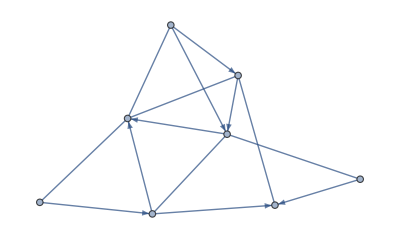
FindPostmanTour[-Graphics-]

```mathematica
FindPostmanTour[RandomWeightedMixedGraph[{8,14},0.68,RandomReal[]&]]
```

```mathematica
FindPostmanTour[RandomWeightedMixedGraph[{8,14},1,RandomReal[]&]]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

```mathematica
Names["*Vertex*"]
```

{DominatorVertexList,EvenVertexList,EvenVertexQ,FindIndependentVertexSet,FindVertexColoring,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,IndependentVertexSetQ,KVertexConnectedComponents,KVertexConnectedGraphQ,OddVertexList,OddVertexQ,VertexAdd,VertexCapacity,VertexChromaticNumber,VertexColors,VertexComponent,VertexConnectivity,VertexContract,VertexCoordinateRules,VertexCoordinates,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexCoverQ,VertexDataCoordinates,VertexDegree,VertexDelete,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInComponentGraph,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexLabeling,VertexLabels,VertexLabelStyle,VertexList,VertexNormals,VertexOutComponent,VertexOutComponentGraph,VertexOutDegree,VertexQ,VertexRenderingFunction,VertexReplace,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexTransitiveGraphQ,VertexWeight,VertexWeightedGraphQ}

```mathematica
FindEdgeCover[-Graphics-]
```

{1<->2,3<->6,5<->4}

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

RandomWeightedMixedGraph::shdw: Symbol RandomWeightedMixedGraph appears in multiple contexts {PeterBurbery`MixedGraphs`,Global`}; definitions in context PeterBurbery`MixedGraphs` may shadow or be shadowed by other definitions.

```mathematica
RandomWeightedMixedGraph[{10,20},1,RandomInteger[{1,3}]&]
```

RandomWeightedMixedGraph[{10,20},1,RandomInteger[{1,3}]&]